## Estimate normal bacteria’s basal growth rate

```mathematica
Transpose[Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\control_final.xlsx"][[1]]]
```

{{0.,0.208883},{0.1,0.206243},{0.2,0.205276},{0.3,0.203973},{0.4,0.2034},{0.5,0.202501},{0.6,0.20204},{0.7,0.202535},{0.8,0.20258},{0.9,0.202456},{1.,0.203141},{1.1,0.204119},{1.2,0.204052},{1.3,0.205726},{1.4,0.207299},{1.5,0.209681},{1.6,0.212164},{1.7,0.214198},{1.8,0.217377},{1.9,0.223389},{2.,0.229793},{2.1,0.241827},{2.2,0.253108},{2.3,0.264355},{2.4,0.273703},{2.5,0.283085},{2.6,0.291591},{2.7,0.300445},{2.8,0.31031},{2.9,0.318557},{3.,0.327613},{3.1,0.336321},{3.2,0.344816},{3.3,0.353782},{3.4,0.36258},{3.5,0.371052},{3.6,0.381793},{3.7,0.391265},{3.8,0.4024},{3.9,0.413265},{4.,0.42322},{4.1,0.440209},{4.2,0.482344},{4.3,0.544411},{4.4,0.61658},{4.5,0.663613},{4.6,0.695209},{4.7,0.71031},{4.8,0.715838},{4.9,0.726759},{5.,0.73158},{5.1,0.737658},{5.2,0.741647},{5.3,0.742804},{5.4,0.744681},{5.5,0.749052},{5.6,0.752007},{5.7,0.756265},{5.8,0.760849},{5.9,0.766052},{6.,0.768669},{6.1,0.773816},{6.2,0.777243},{6.3,0.780928},{6.4,0.784377},{6.5,0.78758},{6.6,0.790377},{6.7,0.793108},{6.8,0.796759},{6.9,0.799366},{7.,0.802928},{7.1,0.804995},{7.2,0.808231},{7.3,0.811804},{7.4,0.813029},{7.5,0.816231},{7.6,0.819231},{7.7,0.821928},{7.8,0.825557},{7.9,0.827816},{8.,0.830074},{8.1,0.832344},{8.2,0.836917},{8.3,0.837422},{8.4,0.839816},{8.5,0.8434},{8.6,0.845726},{8.7,0.848254},{8.8,0.850546},{8.9,0.852669},{9.,0.854265},{9.1,0.857411},{9.2,0.859096},{9.3,0.862366},{9.4,0.864434},{9.5,0.865096},{9.6,0.869344},{9.7,0.869759},{9.8,0.871827},{9.9,0.874164},{10.,0.875007},{10.1,0.878254},{10.2,0.880299},{10.3,0.881928},{10.4,0.884007},{10.5,0.885613},{10.6,0.888782},{10.7,0.889658},{10.8,0.891108},{10.9,0.894658},{11.,0.895007},{11.1,0.896771},{11.2,0.897894},{11.3,0.899928},{11.4,0.901681},{11.5,0.902332},{11.6,0.904771},{11.7,0.906984},{11.8,0.90795},{11.9,0.909995},{12.,0.910523},{12.1,0.912939},{12.2,0.914355},{12.3,0.9154},{12.4,0.917141},{12.5,0.918849},{12.6,0.920186},{12.7,0.921658},{12.8,0.92322},{12.9,0.924984},{13.,0.92731},{13.1,0.929445},{13.2,0.929287},{13.3,0.930265},{13.4,0.932973},{13.5,0.933141},{13.6,0.93604},{13.7,0.936332},{13.8,0.940287},{13.9,0.939141},{14.,0.94095},{14.1,0.942692},{14.2,0.941287},{14.3,0.942265},{14.4,0.94431},{14.5,0.943546},{14.6,0.943962},{14.7,0.945625},{14.8,0.945052},{14.9,0.945838},{15.,0.945535},{15.1,0.946321},{15.2,0.945052},{15.3,0.94513},{15.4,0.946254},{15.5,0.945759},{15.6,0.944074},{15.7,0.945557},{15.8,0.943546},{15.9,0.944276},{16.,0.944355},{16.1,0.943726},{16.2,0.942119},{16.3,0.942321},{16.4,0.941445},{16.5,0.940849},{16.6,0.9414},{16.7,0.941411},{16.8,0.94022},{16.9,0.938714},{17.,0.938692},{17.1,0.938096},{17.2,0.938018},{17.3,0.936669},{17.4,0.937007},{17.5,0.937883},{17.6,0.935074},{17.7,0.934962},{17.8,0.933243},{17.9,0.934164},{18.,0.932456},{18.1,0.931984},{18.2,0.930883},{18.3,0.930759},{18.4,0.929355},{18.5,0.92913},{18.6,0.927973},{18.7,0.927613},{18.8,0.928872},{18.9,0.927962},{19.,0.925759},{19.1,0.926422},{19.2,0.925085},{19.3,0.924714},{19.4,0.922995},{19.5,0.922995},{19.6,0.922894},{19.7,0.922535},{19.8,0.922557},{19.9,0.922164},{20.,0.920254},{20.1,0.919321},{20.2,0.920175},{20.3,0.918198},{20.4,0.918928},{20.5,0.917478},{20.6,0.918108},{20.7,0.915164},{20.8,0.916737},{20.9,0.917018},{21.,0.916377},{21.1,0.913883},{21.2,0.914602},{21.3,0.913456},{21.4,0.913973},{21.5,0.913085},{21.6,0.912602},{21.7,0.910793},{21.8,0.910108},{21.9,0.911344},{22.,0.910018},{22.1,0.910962},{22.2,0.908669},{22.3,0.908726},{22.4,0.908074},{22.5,0.90722},{22.6,0.906377},{22.7,0.906332},{22.8,0.905119},{22.9,0.905119},{23.,0.905523},{23.1,0.905029},{23.2,0.903164},{23.3,0.903108},{23.4,0.90022},{23.5,0.900782},{23.6,0.900119},{23.7,0.899602},{23.8,0.89749},{23.9,0.896827},{24.,0.896467},{24.1,0.895546},{24.2,0.894748},{24.3,0.893804},{24.4,0.894355},{24.5,0.893613},{24.6,0.892445},{24.7,0.892119},{24.8,0.892141},{24.9,0.892052},{25.,0.89022},{25.1,0.888748},{25.2,0.888119},{25.3,0.886939},{25.4,0.885669},{25.5,0.886299},{25.6,0.884827},{25.7,0.884332},{25.8,0.884658},{25.9,0.881861},{26.,0.882523},{26.1,0.880692},{26.2,0.878546},{26.3,0.878164},{26.4,0.878344},{26.5,0.876849},{26.6,0.876928},{26.7,0.87713},{26.8,0.875523},{26.9,0.874243},{27.,0.874726},{27.1,0.871602},{27.2,0.870771},{27.3,0.87395},{27.4,0.870018},{27.5,0.870478},{27.6,0.868962},{27.7,0.868771},{27.8,0.866175},{27.9,0.868905}}

```mathematica
controldata=Transpose[Import["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\control_final.xlsx"][[1]]];
experimentData=Import["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\data_final\\cocktail_growth_data.xlsx"];
TIME=Table[i,{i,0,18,0.1}];
phageA=Transpose[{TIME,experimentData[[4,1]]}];
phageB=Transpose[{TIME,experimentData[[5,1]]}];
phageC=Transpose[{TIME,experimentData[[6,1]]}];
TIME=Table[i,{i,0,27.9,0.1}];
bacteriaControl=controldata;
noLag=Select[bacteriaControl,5.5>#[[1]]≥2&];
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3]==Select[bacteriaControl,#[[1]]==3&][[1,2]]} ,y[t],t][[1,1,2]];
germGrowth2[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3.5]==Select[phageA,#[[1]]==3.5&][[1,2]]} ,y[t],t][[1,1,2]];
germGrowth3[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[4.2]==Select[phageB,#[[1]]==4.2&][[1,2]]} ,y[t],t][[1,1,2]];
germGrowth4[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3.8]==Select[phageC,#[[1]]==3.8&][[1,2]]} ,y[t],t][[1,1,2]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
controldata=Transpose[Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\control_final.xlsx"][[1]]];
experimentData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\data_final\\cocktail_growth_data.xlsx"];
TIME=Table[i,{i,0,18,0.1}];
phageA=Transpose[{TIME,experimentData[[4,1]]}];
phageB=Transpose[{TIME,experimentData[[5,1]]}];
phageC=Transpose[{TIME,experimentData[[6,1]]}];
TIME=Table[i,{i,0,27.9,0.1}];
bacteriaControl=controldata;
noLag=Select[bacteriaControl,5.5>#[[1]]≥2&];
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3]==Select[bacteriaControl,#[[1]]==3&][[1,2]]} ,y[t],t][[1,1,2]];
germGrowth2[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3.5]==Select[phageA,#[[1]]==3.5&][[1,2]]} ,y[t],t][[1,1,2]];
germGrowth3[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[4.2]==Select[phageB,#[[1]]==4.2&][[1,2]]} ,y[t],t][[1,1,2]];
germGrowth4[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3.8]==Select[phageC,#[[1]]==3.8&][[1,2]]} ,y[t],t][[1,1,2]];
```

Import::nffil: File C:\Users\16337\Dropbox\Stan Yu\Phage project\simulation\control_final.xlsx not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File C:\Users\16337\Dropbox\Stan Yu\Phage project\simulation\data_final\cocktail_growth_data.xlsx not found during Import.

Part::partd: Part specification $Failed⟦4,1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,«171»},$Failed⟦4,1⟧} cannot be transposed.

Part::partd: Part specification $Failed⟦5,1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,«171»},$Failed⟦5,1⟧} cannot be transposed.

Part::partd: Part specification $Failed⟦6,1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,«171»},$Failed⟦6,1⟧} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of Transpose[] does not exist.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of Transpose[] does not exist.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of Transpose[] does not exist.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of Transpose[] does not exist.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Select[bacteriaControl,#[[1]]==3&][[1,2]]
```

0.327613

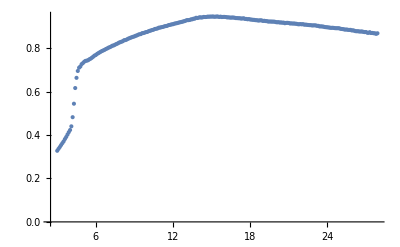

```mathematica
ListPlot[Select[bacteriaControl,#[[1]]≥3&],PlotRange->All]
```

```mathematica
Select[phageA,#[[1]]==3.5&][[1,2]]
```

0.327194

```mathematica
Select[phageB,#[[1]]==4.7&][[1,2]]
```

0.412594

```mathematica
Select[phageC,#[[1]]==4.5&][[1,2]]
```

0.372618

```mathematica
ListPlot[{Select[phageA,#[[1]]>=3.5&],Select[phageB,#[[1]]>=4.2&],Select[phageC,#[[1]]>=3.8&]},PlotLabels->{"a","b","c"},ImageSize->Large]
```

-Graphics-

```mathematica
phageC
```

{{0.,0.209181},{0.1,0.206472},{0.2,0.205931},{0.3,0.204431},{0.4,0.203847},{0.5,0.203576},{0.6,0.203639},{0.7,0.203639},{0.8,0.203535},{0.9,0.203701},{1.,0.204972},{1.1,0.205139},{1.2,0.206056},{1.3,0.205514},{1.4,0.207118},{1.5,0.207493},{1.6,0.207639},{1.7,0.208993},{1.8,0.209097},{1.9,0.210743},{2.,0.211639},{2.1,0.214472},{2.2,0.216347},{2.3,0.21891},{2.4,0.224472},{2.5,0.229201},{2.6,0.235056},{2.7,0.242222},{2.8,0.249785},{2.9,0.257681},{3.,0.263431},{3.1,0.270368},{3.2,0.27666},{3.3,0.281431},{3.4,0.287368},{3.5,0.292931},{3.6,0.297847},{3.7,0.30466},{3.8,0.311076},{3.9,0.317639},{4.,0.32491},{4.1,0.331951},{4.2,0.339806},{4.3,0.347868},{4.4,0.357972},{4.5,0.372618},{4.6,0.396847},{4.7,0.428847},{4.8,0.46766},{4.9,0.506639},{5.,0.544743},{5.1,0.575306},{5.2,0.596701},{5.3,0.608535},{5.4,0.621785},{5.5,0.630951},{5.6,0.641597},{5.7,0.649681},{5.8,0.657472},{5.9,0.666014},{6.,0.673264},{6.1,0.680097},{6.2,0.68516},{6.3,0.689431},{6.4,0.693389},{6.5,0.698201},{6.6,0.702868},{6.7,0.706472},{6.8,0.708576},{6.9,0.711222},{7.,0.715222},{7.1,0.718535},{7.2,0.722326},{7.3,0.724743},{7.4,0.727889},{7.5,0.731451},{7.6,0.733806},{7.7,0.737597},{7.8,0.739764},{7.9,0.742431},{8.,0.744847},{8.1,0.748576},{8.2,0.750306},{8.3,0.752285},{8.4,0.755222},{8.5,0.757618},{8.6,0.757514},{8.7,0.760431},{8.8,0.763347},{8.9,0.765285},{9.,0.767618},{9.1,0.769368},{9.2,0.772306},{9.3,0.774201},{9.4,0.775701},{9.5,0.779181},{9.6,0.779326},{9.7,0.782847},{9.8,0.785264},{9.9,0.786035},{10.,0.788993},{10.1,0.790431},{10.2,0.79241},{10.3,0.793118},{10.4,0.79516},{10.5,0.797056},{10.6,0.799139},{10.7,0.802056},{10.8,0.804347},{10.9,0.803451},{11.,0.805535},{11.1,0.807972},{11.2,0.810764},{11.3,0.810847},{11.4,0.812743},{11.5,0.815889},{11.6,0.818118},{11.7,0.817826},{11.8,0.818306},{11.9,0.821222},{12.,0.822326},{12.1,0.823889},{12.2,0.82516},{12.3,0.826681},{12.4,0.827826},{12.5,0.829139},{12.6,0.830722},{12.7,0.832868},{12.8,0.836618},{12.9,0.836056},{13.,0.837139},{13.1,0.838493},{13.2,0.840056},{13.3,0.840389},{13.4,0.842576},{13.5,0.843264},{13.6,0.844326},{13.7,0.846285},{13.8,0.846181},{13.9,0.847847},{14.,0.848639},{14.1,0.850014},{14.2,0.851514},{14.3,0.85166},{14.4,0.853389},{14.5,0.852764},{14.6,0.855306},{14.7,0.856743},{14.8,0.85641},{14.9,0.856743},{15.,0.857722},{15.1,0.858056},{15.2,0.861743},{15.3,0.861326},{15.4,0.861306},{15.5,0.861097},{15.6,0.86191},{15.7,0.863847},{15.8,0.864764},{15.9,0.865035},{16.,0.866222},{16.1,0.868868},{16.2,0.868681},{16.3,0.86916},{16.4,0.869681},{16.5,0.869014},{16.6,0.869181},{16.7,0.86941},{16.8,0.870306},{16.9,0.87141},{17.,0.870972},{17.1,0.872514},{17.2,0.873285},{17.3,0.871618},{17.4,0.871597},{17.5,0.873243},{17.6,0.871951},{17.7,0.872368},{17.8,0.874785},{17.9,0.87441},{18.,0.872701}}

```mathematica
bacteriaControl
```

{{0.,0.223929},{0.1,0.221518},{0.2,0.220322},{0.3,0.219714},{0.4,0.219134},{0.5,0.219134},{0.6,0.21867},{0.7,0.219286},{0.8,0.219804},{0.9,0.220411},{1.,0.220554},{1.1,0.222116},{1.2,0.223161},{1.3,0.225616},{1.4,0.228598},{1.5,0.231688},{1.6,0.235804},{1.7,0.240161},{1.8,0.247688},{1.9,0.254098},{2.,0.261429},{2.1,0.269625},{2.2,0.278072},{2.3,0.287411},{2.4,0.296697},{2.5,0.305339},{2.6,0.31367},{2.7,0.322464},{2.8,0.331188},{2.9,0.339081},{3.,0.347706},{3.1,0.356572},{3.2,0.364991},{3.3,0.374661},{3.4,0.383714},{3.5,0.394973},{3.6,0.408223},{3.7,0.423706},{3.8,0.438214},{3.9,0.45817},{4.,0.485813},{4.1,0.512259},{4.2,0.53617},{4.3,0.559643},{4.4,0.590366},{4.5,0.619482},{4.6,0.647098},{4.7,0.666313},{4.8,0.679232},{4.9,0.692536},{5.,0.701366},{5.1,0.710411},{5.2,0.717241},{5.3,0.723661},{5.4,0.726563},{5.5,0.730991},{5.6,0.733759},{5.7,0.736232},{5.8,0.740054},{5.9,0.744188},{6.,0.745098},{6.1,0.748482},{6.2,0.749348},{6.3,0.753304},{6.4,0.756973},{6.5,0.758732},{6.6,0.760081},{6.7,0.76175},{6.8,0.764947},{6.9,0.767732},{7.,0.770232},{7.1,0.770866},{7.2,0.773009},{7.3,0.776482},{7.4,0.777723},{7.5,0.778688},{7.6,0.780777},{7.7,0.784188},{7.8,0.785},{7.9,0.789018},{8.,0.795714},{8.1,0.79725},{8.2,0.790866},{8.3,0.787777},{8.4,0.785357},{8.5,0.784625},{8.6,0.785232},{8.7,0.784741},{8.8,0.782536},{8.9,0.7825},{9.,0.780714},{9.1,0.779107},{9.2,0.777456},{9.3,0.775545},{9.4,0.771813},{9.5,0.773331},{9.6,0.786072},{9.7,0.818723},{9.8,0.863197},{9.9,0.913116},{10.,0.949911},{10.1,0.972098},{10.2,0.985563},{10.3,0.993384},{10.4,0.999214},{10.5,1.00286},{10.6,1.00853},{10.7,1.01193},{10.8,1.01419},{10.9,1.01688},{11.,1.01908},{11.1,1.02091},{11.2,1.02475},{11.3,1.02601},{11.4,1.02978},{11.5,1.03046},{11.6,1.03326},{11.7,1.03518},{11.8,1.03663},{11.9,1.03972},{12.,1.03952},{12.1,1.04306},{12.2,1.04407},{12.3,1.04561},{12.4,1.04839},{12.5,1.04903},{12.6,1.05134},{12.7,1.05233},{12.8,1.05496},{12.9,1.05516},{13.,1.05773},{13.1,1.05795},{13.2,1.05914},{13.3,1.06082},{13.4,1.06256},{13.5,1.0651},{13.6,1.06607},{13.7,1.06683},{13.8,1.06888},{13.9,1.06957},{14.,1.07039},{14.1,1.07277},{14.2,1.07294},{14.3,1.07337},{14.4,1.07582},{14.5,1.07609},{14.6,1.0784},{14.7,1.08038},{14.8,1.08065},{14.9,1.08158},{15.,1.08364},{15.1,1.08368},{15.2,1.08463},{15.3,1.08651},{15.4,1.08663},{15.5,1.08788},{15.6,1.08885},{15.7,1.09011},{15.8,1.09054},{15.9,1.09135},{16.,1.09155},{16.1,1.09279},{16.2,1.0946},{16.3,1.09504},{16.4,1.09563},{16.5,1.09613},{16.6,1.09605},{16.7,1.09724},{16.8,1.09778},{16.9,1.09761},{17.,1.09804},{17.1,1.09962},{17.2,1.10101},{17.3,1.0987},{17.4,1.09987},{17.5,1.1017},{17.6,1.10081},{17.7,1.10043},{17.8,1.10049},{17.9,1.10096},{18.,1.10043},{18.1,1.10054},{18.2,1.10131},{18.3,1.10101},{18.4,1.10134},{18.5,1.09996},{18.6,1.10022},{18.7,1.10021},{18.8,1.09941},{18.9,1.09901},{19.,1.10121},{19.1,1.09958},{19.2,1.09887},{19.3,1.09756},{19.4,1.09766},{19.5,1.09716},{19.6,1.09721},{19.7,1.09638},{19.8,1.0956},{19.9,1.09521},{20.,1.09464},{20.1,1.09413},{20.2,1.09333},{20.3,1.0934},{20.4,1.09315},{20.5,1.09054},{20.6,1.09106},{20.7,1.08905},{20.8,1.09104},{20.9,1.08859},{21.,1.08804},{21.1,1.08718},{21.2,1.08654},{21.3,1.08684},{21.4,1.08657},{21.5,1.08574},{21.6,1.08269},{21.7,1.08296},{21.8,1.08321},{21.9,1.08184},{22.,1.08066},{22.1,1.07957},{22.2,1.07841},{22.3,1.07902},{22.4,1.0783},{22.5,1.07779},{22.6,1.0742},{22.7,1.07442},{22.8,1.07462},{22.9,1.07423},{23.,1.07334},{23.1,1.07192},{23.2,1.07083},{23.3,1.06963},{23.4,1.06833},{23.5,1.06701},{23.6,1.06551},{23.7,1.06486},{23.8,1.06363},{23.9,1.06288},{24.,1.05998},{24.1,1.05949},{24.2,1.05873},{24.3,1.05783},{24.4,1.0548},{24.5,1.05324},{24.6,1.05242},{24.7,1.05019},{24.8,1.04899},{24.9,1.04761},{25.,1.04759},{25.1,1.04588},{25.2,1.04346},{25.3,1.04168},{25.4,1.04206},{25.5,1.04041},{25.6,1.03936},{25.7,1.03731},{25.8,1.03591},{25.9,1.03578},{26.,1.03313},{26.1,1.03137},{26.2,1.03026},{26.3,1.02867},{26.4,1.02596},{26.5,1.02372},{26.6,1.02404},{26.7,1.02446},{26.8,1.02347},{26.9,1.02182},{27.,1.02006},{27.1,1.01866},{27.2,1.01593},{27.3,1.01563},{27.4,1.01212},{27.5,1.01397},{27.6,1.01369},{27.7,1.01086},{27.8,1.01037},{27.9,1.00911}}

```mathematica
para=FindFit[noLag,{germGrowth[k,r,t],0.881>r>0.88,1.1>k>0},{{k,0.9},{r,0.88}},t]
```

{k→0.913762,r→0.880001}

```mathematica
para2=FindFit[Select[phageA,#[[1]]>=3.5&],{germGrowth2[0.88,r,t],r>0.77},{{r,0.89}},t]
```

{r→0.77}

```mathematica
para3=FindFit[Select[phageB,#[[1]]>=4.2&],{germGrowth3[0.998,r,t],r>0.8},{{r,0.88}},t]
```

{r→0.8}

```mathematica
para4=FindFit[Select[phageC,#[[1]]>=3.8&],{germGrowth4[0.88,r,t],r>0.81},{{r,0.88}},t]
```

{r→0.81}

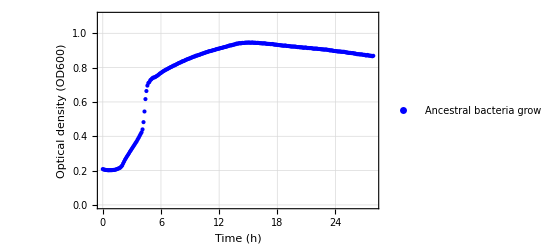

```mathematica
ListPlot[bacteriaControl,PlotLegends->Placed[LineLegend[{"Ancestral bacteria\ngrowth data"}],{0.15,0.9}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,14},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{0,27.9},{0,1.1}},ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"}]
```

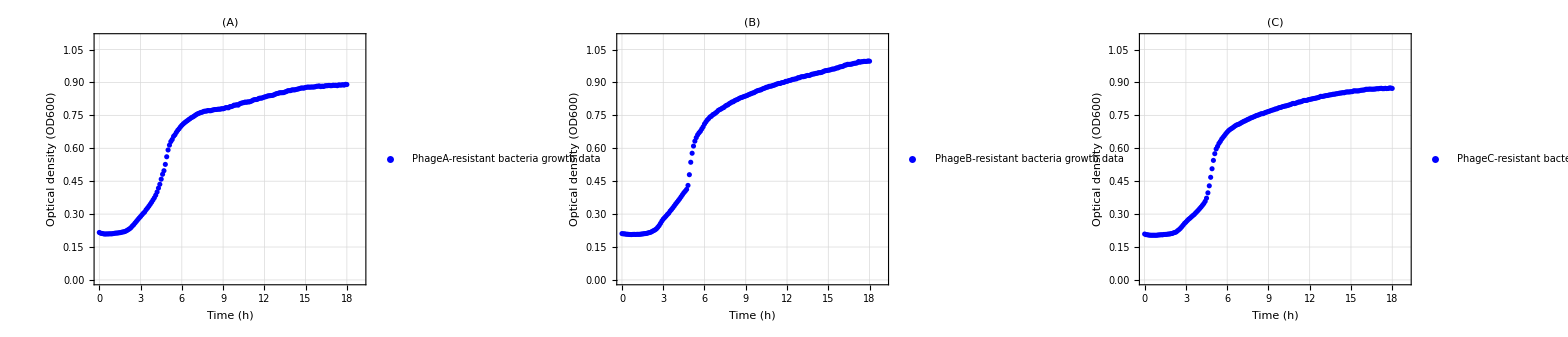

```mathematica
GraphicsGrid[{{ListPlot[phageA,PlotLegends->Placed[LineLegend[{"PhageA-resistant\nbacteria growth data"}],{0.15,0.9}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,14},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{0,19},{0,1.1}},ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLabel->"(A)"],ListPlot[phageB,PlotLegends->Placed[LineLegend[{"PhageB-resistant\nbacteria growth data"}],{0.15,0.9}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,14},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{0,19},{0,1.1}},ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLabel->"(B)"],ListPlot[phageC,PlotLegends->Placed[LineLegend[{"PhageC-resistant\nbacteria growth data"}],{0.15,0.9}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,14},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{0,19},{0,1.1}},ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLabel->"(C)"]}},Alignment->Center,Spacings->0]
```

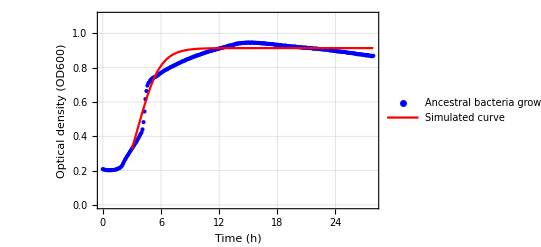

```mathematica
Anfit=Show[ListPlot[bacteriaControl,PlotLegends->Placed[LineLegend[{"Ancestral bacteria\ngrowth data"}],{0.75,0.5}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"},PlotRange->All],Plot[germGrowth[k,r,t]/.para,{t,3,27.9},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.75,0.37}],PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Frame->True,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotRange->{{0,27.9},{0,1.1}}]
```

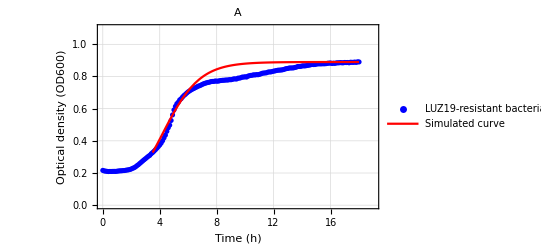

```mathematica
Afit=Show[ListPlot[phageA,PlotLegends->Placed[LineLegend[{"LUZ19-resistant\nbacteria growth data"}],{0.75,0.5}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"},PlotRange->All],Plot[germGrowth2[0.89,r,t]/.para2,{t,3.5,18},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.75,0.37}],PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Frame->True,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotRange->{{0,19},{0,1.1}},PlotLabel->"A"]
```

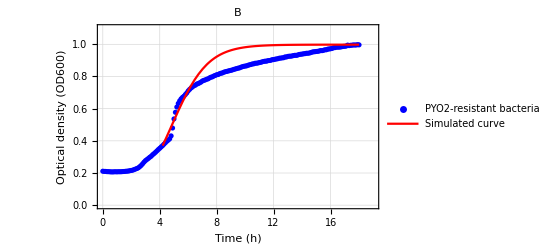

```mathematica
Bfit=Show[ListPlot[phageB,PlotLegends->Placed[LineLegend[{"PYO2-resistant\nbacteria growth data"}],{0.75,0.5}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"},PlotRange->All],Plot[germGrowth3[0.998,r,t]/.para3,{t,4.2,18},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.75,0.37}],PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Frame->True,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotRange->{{0,19},{0,1.1}},PlotLabel->"B"]
```

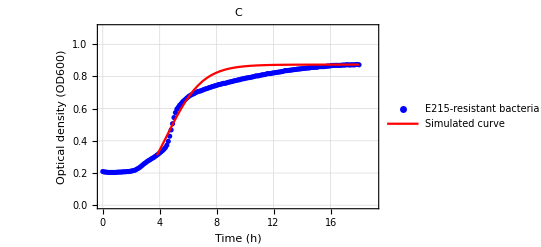

```mathematica
Cfit=Show[ListPlot[phageC,PlotLegends->Placed[LineLegend[{"E215-resistant\nbacteria growth data"}],{0.75,0.5}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"},PlotRange->All],Plot[germGrowth4[0.874,r,t]/.para4,{t,3.8,18},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.75,0.37}],PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Frame->True,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotRange->{{0,19},{0,1.1}},PlotLabel->"C"]
```

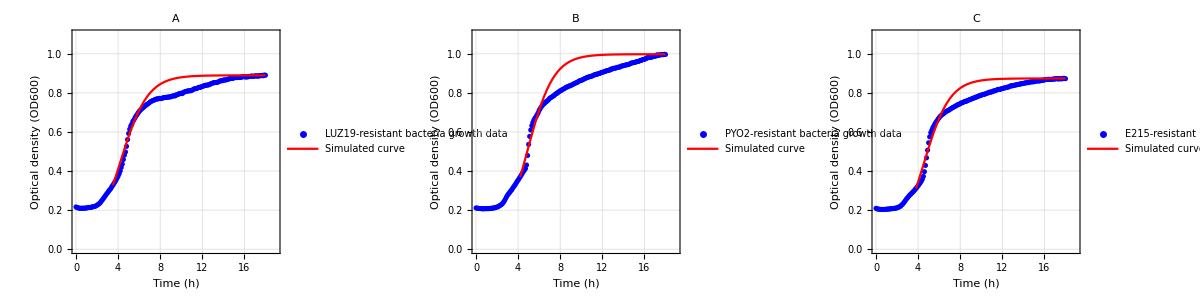

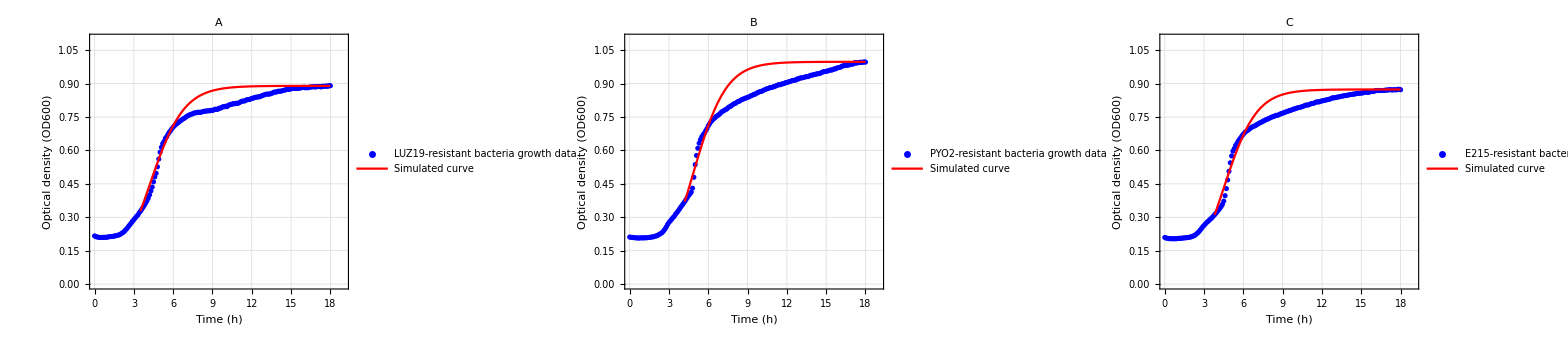

```mathematica
GraphicsGrid[{{-Graphics-,-Graphics-,-Graphics-}},ImageSize->3000]
```

## Estimate phage-A-specific parameter values

### ra

```mathematica
experimentData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\experimentNew.xlsx"];
```

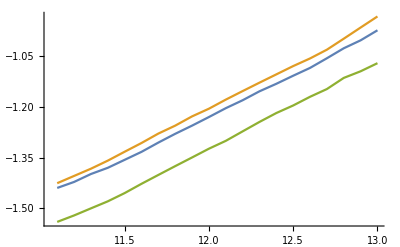

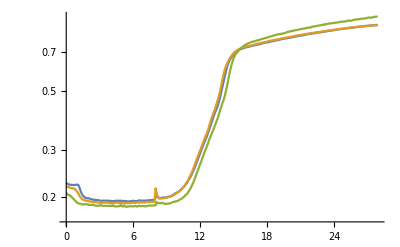

```mathematica
experimentData=Import["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\experimentNew.xlsx"];
TIME=Table[i,{i,0,27.9,0.1}];
phageAMOI01=Transpose[{TIME,experimentData[[1,1]]}];
phageAMOI1=Transpose[{TIME,experimentData[[2,1]]}];
phageAMOI10=Transpose[{TIME,experimentData[[3,1]]}];
expA01=Select[phageAMOI01,11.1<=#[[1]]≤13&];
expA1=Select[phageAMOI1,11.1<=#[[1]]≤13&];
expA10=Select[phageAMOI10,11.1<=#[[1]]≤13&];
logExpA01=Replace[expA01,{x_,y_}->{x,Log[y]},1];
logExpA1=Replace[expA1,{x_,y_}->{x,Log[y]},1];
logExpA10=Replace[expA10,{x_,y_}->{x,Log[y]},1];
ListLinePlot[{logExpA01,logExpA1,logExpA10}]
ListLogPlot[{phageAMOI01,phageAMOI1,phageAMOI10},Joined->True]
```

```mathematica
linear1=LinearModelFit[logExpA01,{1,t},t]
linear1["ANOVATable"]
linear2=LinearModelFit[logExpA1,{1,t},t]
linear2["ANOVATable"]
linear3=LinearModelFit[logExpA10,{1,t},t]
linear3["ANOVATable"]
```

FittedModel[-8.62028+0.53644 t]

| DF | SS | MS | F-Statistic | P-Value
t | 1 | 1.91366 | 1.91366 | 5978.55 | 3.67455×10^-24
Error | 18 | 0.00576157 | 0.000320087 |  | 
Total | 19 | 1.91942 |  |  |

FittedModel[-9.29502+0.602517 t]

| DF | SS | MS | F-Statistic | P-Value
t | 1 | 2.41413 | 2.41413 | 4181.29 | 9.0779×10^-23
Error | 18 | 0.0103926 | 0.000577365 |  | 
Total | 19 | 2.42452 |  |  |

FittedModel[-9.62721+0.633488 t]

| DF | SS | MS | F-Statistic | P-Value
t | 1 | 2.66869 | 2.66869 | 2390.55 | 1.35332×10^-20
Error | 18 | 0.0200943 | 0.00111635 |  | 
Total | 19 | 2.68878 |  |  |

```mathematica
(* Approximate value for ra, used as guess in findfit *)
```

```mathematica
Mean[{0.5364401982391751 ,0.602517499659348,0.6334877403684634}]
```

0.590815

#### Fitting using data from phage A only experiment

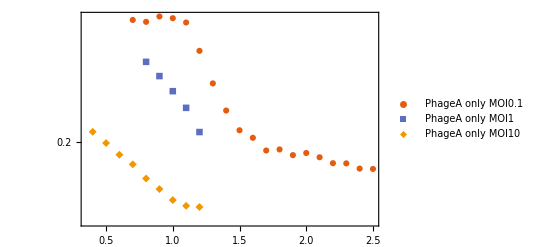

```mathematica
experimentData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\experimentNew.xlsx"];
TIME=Table[i,{i,0,27.9,0.1}];
phageAMOI01=Transpose[{TIME,experimentData[[1,1]]}];
phageAMOI1=Transpose[{TIME,experimentData[[2,1]]}];
phageAMOI10=Transpose[{TIME,experimentData[[3,1]]}];
(* Different ranges for different MOI. Different lags? *)
beginA01=Select[phageAMOI01,0.7<=#[[1]]≤2.5&];
beginA1=Select[phageAMOI1,0.8<=#[[1]]≤1.2&];
beginA10=Select[phageAMOI10,0.4<=#[[1]]≤1.2&];g1=ListLogPlot[{beginA01,beginA1,beginA10},PlotMarkers->Automatic,PlotLegends->Placed[PointLegend[{"PhageA only MOI0.1","PhageA only MOI1","PhageA only MOI10"},LegendFunction->Framed],{0.2,0.2}],Frame->True,PlotTheme->"Scientific",PlotRange->All,ImageSize->Full]
```

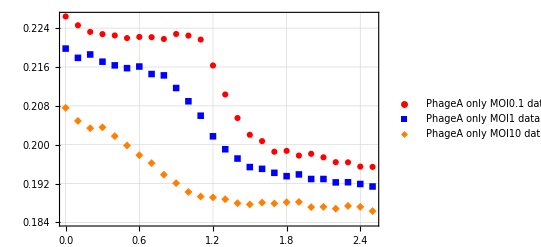

```mathematica
earlyData=ListPlot[{Select[phageAMOI01,0<=#[[1]]≤2.5&],Select[phageAMOI1,0<=#[[1]]≤2.5&],Select[phageAMOI10,0<=#[[1]]≤2.5&]},PlotMarkers->Automatic,PlotLegends->Placed[PointLegend[{"PhageA only MOI0.1 data","PhageA only MOI1 data","PhageA only MOI10 data"}],{0.2,0.2}],Frame->True,PlotTheme->"Detailed",BaseStyle->{Bold,14},FrameStyle->{Bold,Black},GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotStyle->{Red,Blue,Orange}]
```

```mathematica
(* Models for different MOI, used to estimate b, h, s, and p *)
PH[a_,k_,b_,h_,s_,p_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+0.8772547720626924*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+0.8772547720626924*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
sol1=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[0.7]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
sol2=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[0.8]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
sol3=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[0.4]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
model1[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=sol1[a,k,b,h,s,p,B0,MOI][t]
model2[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=sol2[a,k,b,h,s,p,B0,MOI][t]
model3[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=sol3[a,k,b,h,s,p,B0,MOI][t]
```

```mathematica
(* Initial bacteria values *)
MOI01INI=Select[phageAMOI01,0.7==#[[1]]&][[1,2]];
MOI1INI=Select[phageAMOI1,0.8==#[[1]]&][[1,2]];
MOI10INI=Select[phageAMOI10,0.4==#[[1]]&][[1,2]];
```

ParametricNDSolveValue::ndsz: At t == 0.678878, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At t == 0.678879, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At t == 0.678878, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

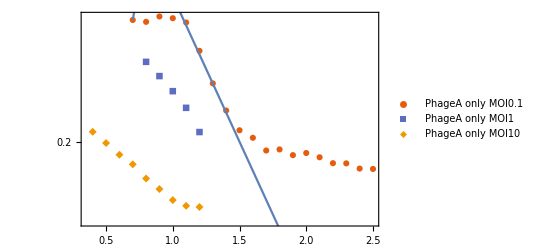

{b→460.,s→0.250001}

```mathematica
(* Fit to phageA MOI01 data 1.1 to 5 hours *)
fitModel1=NonlinearModelFit[beginA01,{model1[0,1,b,100,s,0.09,MOI01INI,0.1,t],b==460,0.25<s<1},{b,s},t];
Show[g1,LogPlot[fitModel1[t],{t,0.7,2.5}]]
fitModel1[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 0.790001, step size is effectively zero; singularity or stiff system suspected.

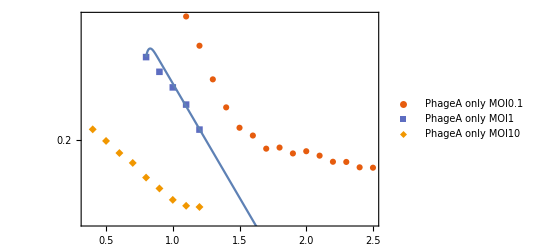

{b→460.,s→0.19}

```mathematica
fitModel2=NonlinearModelFit[beginA1,{model2[0,1,b,100,s,0.09,MOI1INI,1,t],b==460,s==0.19},{b,s},t];
Show[g1,LogPlot[fitModel2[t],{t,0.8,5}]]
fitModel2[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 0.389561, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

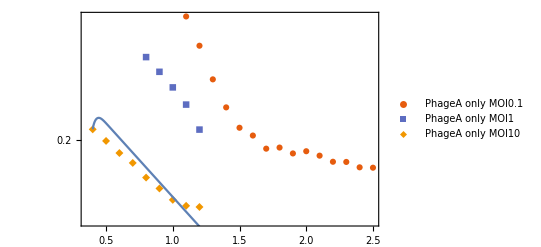

{b→460.,s→0.122835}

```mathematica
fitModel3=NonlinearModelFit[beginA10,{model3[0,1,b,100,s,0.09,MOI10INI,1,t],b==460,0.1<s<3},{b,s},t];
Show[g1,LogPlot[fitModel3[t],{t,0.4,1.2}]]
fitModel3[[1,2]]
```

```mathematica
(* Estimated value for b *)
Mean[{278.29302358448314,269.29353987583715,283.50759875150936}]
```

277.031

```mathematica
(* Estimated value for s*)
Mean[{2.940544982380593,2.989984068243238,2.9947033290569367}]
```

2.97508

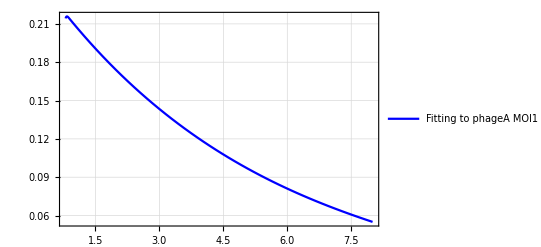

```mathematica
GphageAMOI1Early=Plot[{fitModel2[t]},{t,0.8,8},PlotStyle->Blue,PlotLegends->Placed[LineLegend[{"Fitting to phageA MOI1 data"}],{0.2,0.3}],PlotTheme->"Detailed",ImageSize->Full,BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
```

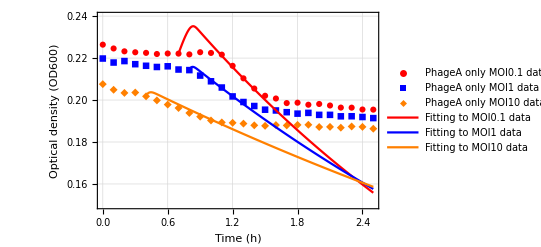

```mathematica
Show[earlyData,Plot[{fitModel1[t]},{t,0.7,2.5},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Fitting to MOI0.1 data"}],{0.5,0.3}]],Plot[{fitModel2[t]},{t,0.8,2.5},PlotStyle->Blue,PlotLegends->Placed[LineLegend[{"Fitting to MOI1 data"}],{0.5,0.2}]],Plot[{fitModel3[t]},{t,0.4,2.5},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Fitting to MOI10 data"}],{0.5,0.1}]],Frame->True,PlotTheme->"Scientific",ImageSize->Full,BaseStyle->{Bold,14},FrameStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},PlotRange->{{0,2.5},{0.15,0.24}}]
```

```mathematica
PH2[a_,k_,b_,h_,s_,p_,ra_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+ra*Br*(1-(B+Br)/k),-p*P+h*s*Bi,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+ra*Br*(1-(B+Br)/k)};
```

```mathematica
Remove[s]
```

```mathematica
X[t]
```

{B[t],Bi[t],Br[t],P[t],Bt[t]}

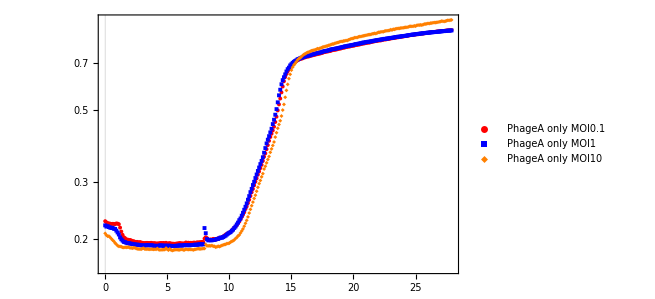

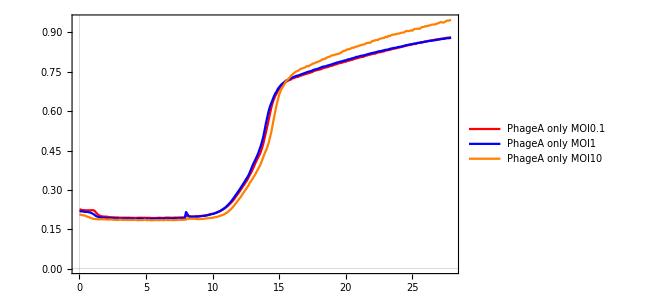

```mathematica
(* Models for different MOI, used to estimate a *)
PH2[a_,k_,b_,h_,s_,p_,ra_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+ra*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+ra*Br*(1-(B+Br)/k)};
stateVar2={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar2[t]];
sol4=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,ra]/.Thread[stateVar2->X[t]])},X[1.1]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,ra,B0,MOI}];
sol5=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,ra]/.Thread[stateVar2->X[t]])},X[0.8]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,ra,B0,MOI}];
solFinal=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,ra]/.Thread[stateVar2->X[t]])},X[0.8]=={B0,0,0,B0*MOI,B0}},{B[t],Bi[t],Br[t],Bt[t]},{t,0.8,27.9},{a,k,b,h,s,p,ra,B0,MOI}];
sol5new=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,ra]/.Thread[stateVar2->X[t]])},X[0.8]=={B0,0,0,B0*MOI,B0}},{B,Br},{t,0,27.9},{a,k,b,h,s,p,ra,B0,MOI}];
sol6=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,ra]/.Thread[stateVar2->X[t]])},X[0.4]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,ra,B0,MOI}];
model4[a_,k_,b_,h_,s_,p_,ra_,B0_,MOI_,t_]:=sol4[a,k,b,h,s,p,ra,B0,MOI][t]
model5[a_,k_,b_,h_,s_,p_,ra_,B0_,MOI_,t_]:=sol5[a,k,b,h,s,p,ra,B0,MOI][t]
model6[a_,k_,b_,h_,s_,p_,ra_,B0_,MOI_,t_]:=sol6[a,k,b,h,s,p,ra,B0,MOI][t]
afterA01=Select[phageAMOI01,1.1<=#[[1]]&];
afterA1=Select[phageAMOI1,0.8<=#[[1]]&];
afterA10=Select[phageAMOI10,0.4<=#[[1]]&];
MOI01INI=Select[phageAMOI01,1.1==#[[1]]&][[1,2]];
MOI1INI=Select[phageAMOI1,0.8==#[[1]]&][[1,2]];
MOI10INI=Select[phageAMOI10,0.4==#[[1]]&][[1,2]];
g2=ListLogPlot[{phageAMOI01,phageAMOI1,phageAMOI10},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageA only MOI0.1","PhageA only MOI1","PhageA only MOI10"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
g3=ListLinePlot[{phageAMOI01,phageAMOI1,phageAMOI10},PlotLegends->Placed[LineLegend[{"PhageA only MOI0.1","PhageA only MOI1","PhageA only MOI10"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
```

```mathematica
fitModel4=NonlinearModelFit[afterA01,{model4[0.008,0.625,277.3725714997275,100,2.975335485731218,0.08,ra,MOI01INI,0.1,t],0.7<ra<0.75},ra,t];
```

ParametricNDSolveValue::ndsz: At t == 0.965728, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

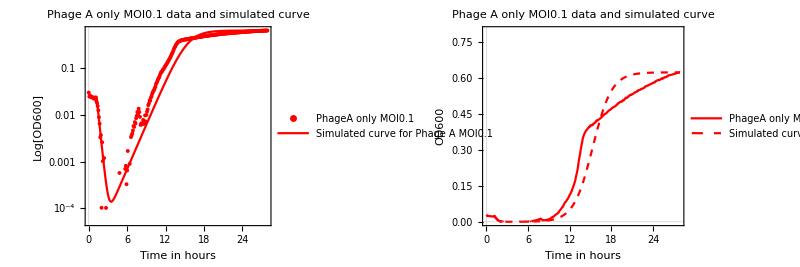

{ra→0.73}

```mathematica
g4=GraphicsGrid[{{Show[ListLogPlot[{phageAMOI01},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageA only MOI0.1"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[fitModel4[t],{t,1.1,27.9},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage A MOI0.1"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific"],PlotLabel->"Phage A only MOI0.1 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"}],Show[ListLinePlot[{phageAMOI01},PlotLegends->Placed[LineLegend[{"PhageA only MOI0.1"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black},PlotRange->{{0,27.9},{0,0.8}}],Plot[fitModel4[t],{t,1.1,27.9},PlotStyle->{Dashed,Red},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage A MOI0.1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage A only MOI0.1 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full]
fitModel4[[1,2]]
```

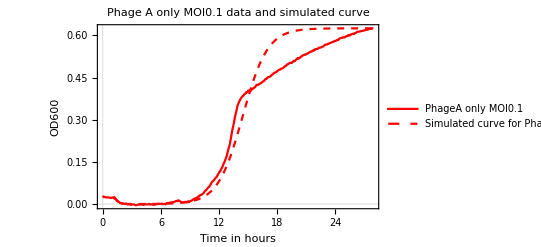

```mathematica
singlePhageG1=Show[ListLinePlot[{phageAMOI01},PlotLegends->Placed[LineLegend[{"PhageA only MOI0.1"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[fitModel4[t],{t,1.1,27.9},PlotStyle->{Dashed,Red},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage A MOI0.1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage A only MOI0.1 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
fitModel5=NonlinearModelFit[afterA1,{model5[a,0.88,460,100,0.19,0.09,ra,MOI1INI,1,t],ra==0.77,a>0.01},{ra,{a,0.027}},t];
```

ParametricNDSolveValue::ndsz: At t == 0.790003, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

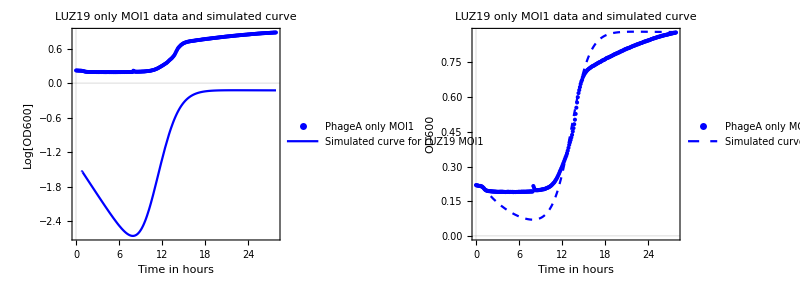

{ra→0.77,a→0.0170428}

```mathematica
g5=GraphicsGrid[{{Show[ListPlot[{phageAMOI1},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageA only MOI1"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Blue},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[fitModel5[t],{t,0.8,27.9},PlotStyle->Blue,
PlotLegends->Placed[LineLegend[{"Simulated curve for\nLUZ19 MOI1"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific"],PlotLabel->"LUZ19 only MOI1 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"},PlotRange-> All],Show[ListPlot[{phageAMOI1},PlotLegends->Placed[LineLegend[{"PhageA only MOI1"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Blue},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[fitModel5[t],{t,0.8,27.9},PlotStyle->{Dashed,Blue},PlotLegends->Placed[LineLegend[{"Simulated curve for\nLUZ19 MOI1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"LUZ19 only MOI1 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full,Frame->True,Alignment->Center,Spacings->0,PlotRange-> {{0,27.9},{0,1}}]
fitModel5[[1,2]]
```

```mathematica
{a,{b,c,d}}
```

{a,{b,c,d}}

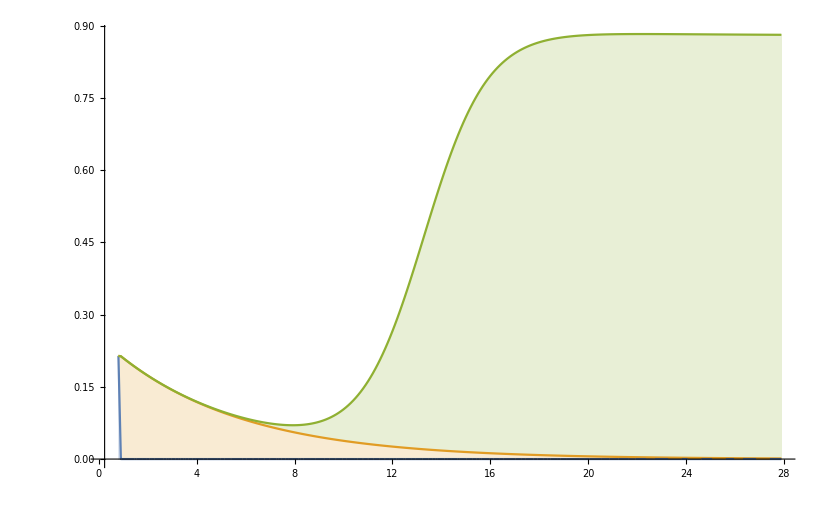

```mathematica
StackedListPlot[Transpose[Table[Map[{t,#}&,Evaluate[(solFinal[a,0.88,460,100,0.19,0.09,ra,MOI1INI,1]/.fitModel5[[1,2]])[[1;;3]]]],{t,0.8,27.9,0.1}]]]
```

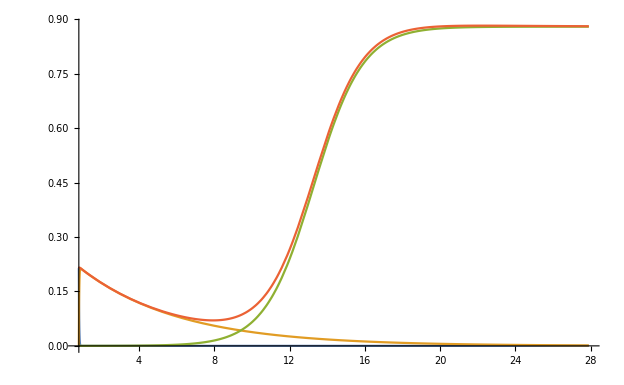

```mathematica
Plot[Evaluate[solFinal[a,0.88,460,100,0.19,0.09,ra,MOI1INI,1]/.fitModel5[[1,2]]],{t,0.8,27.9}]
```

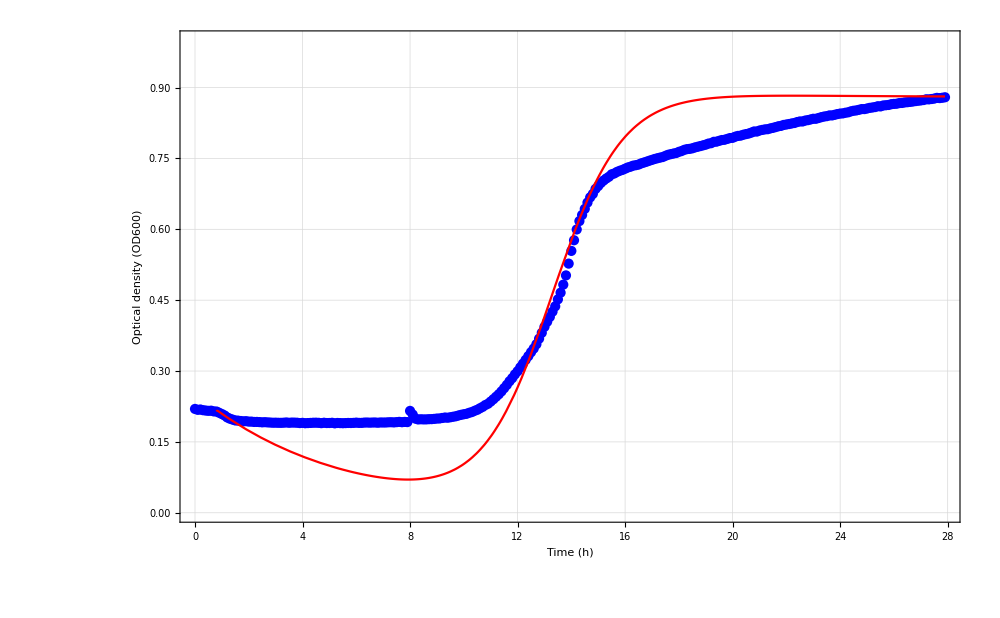

```mathematica
gf11=Show[ListPlot[{phageAMOI1},PlotLegends->Placed[PointLegend[{Directive[Blue,AbsolutePointSize[10]]},{"LUZ19-only-MOI1 Bacteria data"}],{0.25,0.6}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,23},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Plot[fitModel5[t],{t,0.8,27.9},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated bacteria"}],{0.25,0.6}],PlotTheme->"Detailed",BaseStyle->{Bold,25,FontFamily->"Times"},FrameStyle->{Bold,Black},GridLines->Automatic,BaseStyle->{Bold,14,FontFamily->"Times"},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->1000,PlotRange-> {{0,27.9},{0,1}}]
```

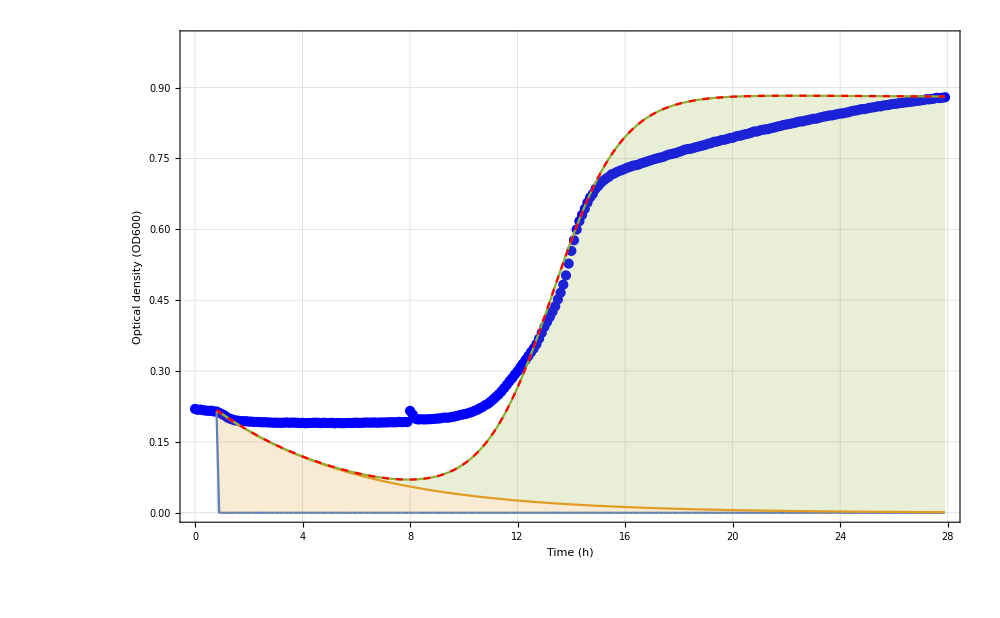

```mathematica
gf12=Show[ListPlot[{phageAMOI1},PlotLegends->Placed[PointLegend[{Directive[Blue,AbsolutePointSize[10]]},{"LUZ19-only-MOI1 Bacteria data"}],{0.25,0.6}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,23},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],StackedListPlot[Transpose[Table[Map[{t,#}&,Evaluate[(solFinal[a,0.88,460,100,0.19,0.09,ra,MOI1INI,1]/.fitModel5[[1,2]])[[1;;3]]]],{t,0.8,27.9,0.1}]],PlotLegends->Placed[SwatchLegend[{"Ancestral bacteria","Infected bacteria","Resistant bacteria"}],{0.25,0.6}],LabelStyle->{FontFamily->"Times"}],Plot[fitModel5[t],{t,0.8,27.9},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{"Simulated bacteria"}],{0.25,0.6}],PlotTheme->"Detailed",BaseStyle->{Bold,25},FrameStyle->{Bold,Black},GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->1000,PlotRange-> {{0,27.9},{0,1}}]
```

```mathematica
gf1=Grid[{{Style["A",FontFamily->"Times",FontSize->30]},{gf11},{gf12}}]
```

A
-Graphics-
-Graphics-

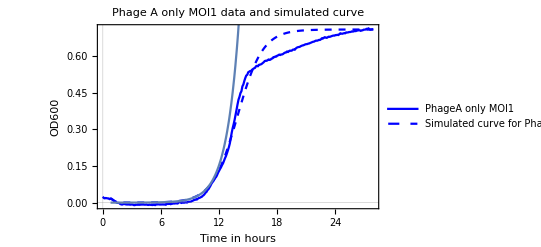

```mathematica
singlePhageG2=Show[ListLinePlot[{phageAMOI1},PlotLegends->Placed[LineLegend[{"PhageA only MOI1"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Blue},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[fitModel5[t],{t,0.8,27.9},PlotStyle->{Dashed,Blue},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage A MOI1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],Plot[0.000015*E^((0.77+0.09/(277*100)*0.027)*t),{t,0.8,27.9},PlotRange->All],PlotLabel->"Phage A only MOI1 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
Through[sol5new[0.027,0.88,460,100,0.17,0.09,0.77,MOI1INI,1][5]]
```

{9.75938×10^-11,0.00139147}

```mathematica
fitModel5[0.8]
```

0.0164528

```mathematica
MOI1INI*0.027*0.1
```

0.0000444226

```mathematica
0.000015*E^((0.77+0.09/(277*100)*0.027)*0.8)
```

0.0000277726

```mathematica
0.09/(277*100)*0.027
```

8.77256×10^-8

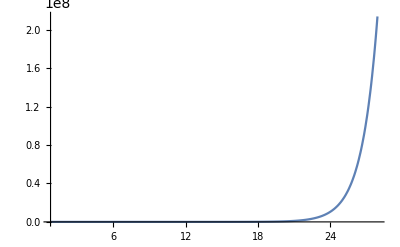

```mathematica
Plot[0.1*E^((0.77+0.09/(277*100)*0.027)*t),{t,0.8,27.9},PlotRange->All]
```

```mathematica
fitModel6=NonlinearModelFit[afterA10,{model6[0.008,0.74,277.3725714997275,100,2.975335485731218,0.09,ra,MOI10INI,1,t],0.77<ra<0.78},ra,t];
```

ParametricNDSolveValue::ndsz: At t == 0.288376, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

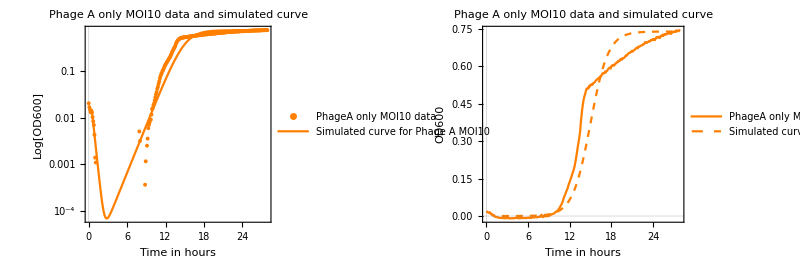

{ra→0.78}

```mathematica
g6=GraphicsGrid[{{Show[ListLogPlot[{phageAMOI10},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageA only MOI10 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[fitModel6[t],{t,0.4,27.9},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage A MOI10"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific"],PlotLabel->"Phage A only MOI10 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"},PlotRange->All],Show[ListLinePlot[{phageAMOI10},PlotLegends->Placed[LineLegend[{"PhageA only MOI10 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[fitModel6[t],{t,0.4,27.9},PlotStyle->{Dashed,Orange},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage A MOI10"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage A only MOI10 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full]
fitModel6[[1,2]]
```

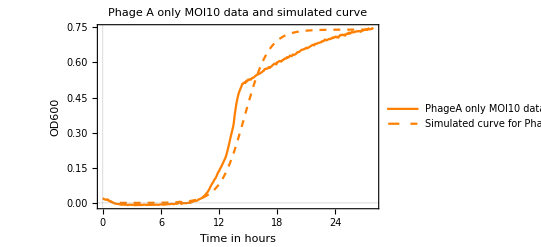

```mathematica
singlePhageG3=Show[ListLinePlot[{phageAMOI10},PlotLegends->Placed[LineLegend[{"PhageA only MOI10 data"},LegendFunction->Framed],{0.75,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[fitModel6[t],{t,0.4,27.9},PlotStyle->{Dashed,Orange},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage A MOI10"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage A only MOI10 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
(* Estimated value for mutation rate(mutate to phageA-resistant)*)
Mean[{0.02467596629360689,0.019187907363862885,0.024999519798104046}]
```

0.0229545

```mathematica
(* Estimated value for ra *)
Mean[{0.7299999924120847,0.8,0.78}]
```

0.77

```mathematica
GraphicsGrid[{{g4},{g5},{g6}},Alignment->Center,Spacings->0,Frame->True,ImageSize->Full]
```

-Graphics-

## Estimate phage-B-specific parameter values

### rb

```mathematica
expB01=Select[phageBMOI01,13<=#[[1]]≤15&];
expB1=Select[phageBMOI1,13<=#[[1]]≤15&];
expB10=Select[phageBMOI10,13<=#[[1]]≤15&];
logExpB01=Replace[expB01,{x_,y_}->{x,Log[y]},1];
logExpB1=Replace[expB1,{x_,y_}->{x,Log[y]},1];
logExpB10=Replace[expB10,{x_,y_}->{x,Log[y]},1];
ListLogPlot[{phageBMOI01,phageBMOI1,phageBMOI10},Joined->True,PlotLegends->{"MOI0.1","MOI1","MOI10"}]
ListLinePlot[{logExpB01,logExpB1,logExpB10}]
```

Select::normal: Nonatomic expression expected at position 1 in Select[phageBMOI01,13≤#1⟦1⟧≤15&].

Select::normal: Nonatomic expression expected at position 1 in Select[phageBMOI1,13≤#1⟦1⟧≤15&].

Select::normal: Nonatomic expression expected at position 1 in Select[phageBMOI10,13≤#1⟦1⟧≤15&].

-Graphics-

Select::normal: Nonatomic expression expected at position 1 in Select[phageBMOI01,13.≤#1⟦1⟧≤15.&].

Select::normal: Nonatomic expression expected at position 1 in Select[phageBMOI1,13.≤#1⟦1⟧≤15.&].

Select::normal: Nonatomic expression expected at position 1 in Select[phageBMOI10,13.≤#1⟦1⟧≤15.&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

-Graphics-

```mathematica
linear1=LinearModelFit[logExpB01,{1,t},t]
linear1["ANOVATable"]
linear2=LinearModelFit[logExpB1,{1,t},t]
linear2["ANOVATable"]
linear3=LinearModelFit[logExpB10,{1,t},t]
linear3["ANOVATable"]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Select[phageBMOI01,13≤#1⟦1⟧≤15&],{1,t},t]

LinearModelFit[Select[phageBMOI01,13≤#1⟦1⟧≤15&],{1,t},t][ANOVATable]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Select[phageBMOI1,13≤#1⟦1⟧≤15&],{1,t},t]

LinearModelFit[Select[phageBMOI1,13≤#1⟦1⟧≤15&],{1,t},t][ANOVATable]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Select[phageBMOI10,13≤#1⟦1⟧≤15&],{1,t},t]

LinearModelFit[Select[phageBMOI10,13≤#1⟦1⟧≤15&],{1,t},t][ANOVATable]

```mathematica
Mean[{0.6261622776470807,0.6617650507813915 ,0.7471335578274599}]
```

0.678354

#### Fitting using data from phage B only experiment

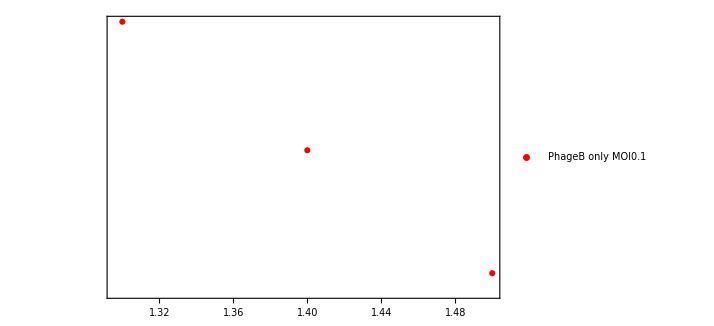

```mathematica
experimentData=Import["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\experimentNew.xlsx"];
TIME=Table[i,{i,0,27.9,0.1}];
phageBMOI01=Transpose[{TIME,experimentData[[4,1]]}];
phageBMOI1=Transpose[{TIME,experimentData[[5,1]]}];
phageBMOI10=Transpose[{TIME,experimentData[[6,1]]}];
beginB01=Select[phageBMOI01,1.6<=#[[1]]≤2.4&];
beginB1=Select[phageBMOI1,1.3<=#[[1]]≤1.5&];
beginB10=Select[phageBMOI10,0.7<=#[[1]]≤1.7&];PBg1=ListLogPlot[{beginB1},PlotMarkers->Automatic,PlotLegends->Placed[PointLegend[{"PhageB only MOI0.1","PhageB only MOI1","PhageB only MOI10"},LegendFunction->Framed],{0.2,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange}]
```

```mathematica
PH[a_,k_,b_,h_,s_,p_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+0.8772547720626924*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+0.8772547720626924*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
PBsol1=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[1.6]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
PBsol2=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[1.3]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
PBsol3=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[0.7]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
PBmodel1[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=PBsol1[a,k,b,h,s,p,B0,MOI][t]
PBmodel2[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=PBsol2[a,k,b,h,s,p,B0,MOI][t]
PBmodel3[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=PBsol3[a,k,b,h,s,p,B0,MOI][t]
```

```mathematica
(* Initial bacteria values *)
PBMOI01INI=Select[phageBMOI01,1.6==#[[1]]&][[1,2]];
PBMOI1INI=Select[phageBMOI1,1.3==#[[1]]&][[1,2]];
PBMOI10INI=Select[phageBMOI10,0.7==#[[1]]&][[1,2]];
```

ParametricNDSolveValue::ndsz: At t == 1.25244, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At t == 1.25245, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At t == 1.25244, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

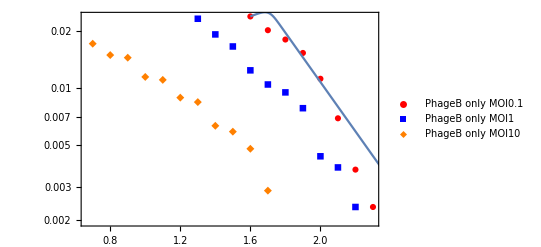

{b→277.,s→2.9934}

```mathematica
PBfitModel1=NonlinearModelFit[beginB01,{PBmodel1[0,1,b,100,s,0.09,PBMOI01INI,0.1,t],b==277,0<s<3},{b,s},t];
Show[PBg1,LogPlot[PBfitModel1[t],{t,1.6,2.4}]]
PBfitModel1[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 1.29028, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

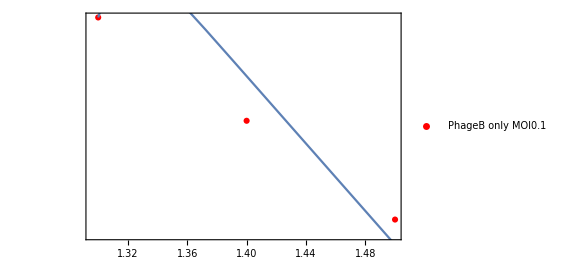

{b→460.,s→0.252181}

```mathematica
PBfitModel2=NonlinearModelFit[beginB1,{PBmodel2[0,1,b,100,s,0.09,PBMOI1INI,1,t],b==460,0<s},{b,s},t];
Show[PBg1,LogPlot[PBfitModel2[t],{t,1.3,2.2}]]
PBfitModel2[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 0.619856, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

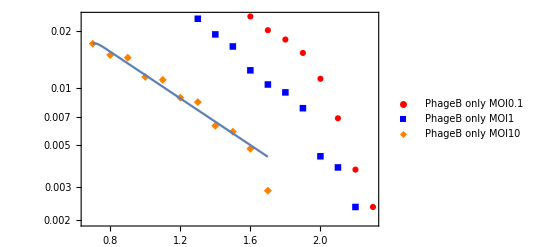

{b→277.,s→1.4172}

```mathematica
PBfitModel3=NonlinearModelFit[beginB10,{PBmodel3[0,1,b,100,s,0.09,PBMOI10INI,10,t],b==277,0<s<3},{b,s},t];
Show[PBg1,LogPlot[PBfitModel3[t],{t,0.7,1.7}]]
PBfitModel3[[1,2]]
```

```mathematica
Mean[{334.5245442504598,324.65273103451716,269.31594362029426}]
```

309.498

```mathematica
Mean[{2.9761581747874795,2.4973376745479787,1.4171960399590724}]
```

2.2969

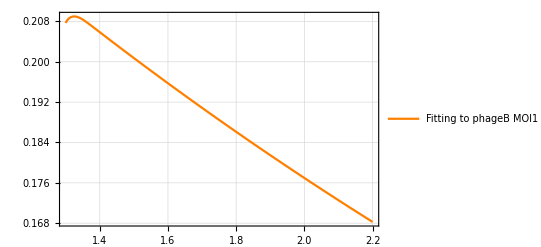

```mathematica
GphageBMOI1Early=Plot[{PBfitModel2[t]},{t,1.3,2.2},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Fitting to phageB MOI1 data"}],{0.2,0.2}],PlotTheme->"Detailed",ImageSize->Full,BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
```

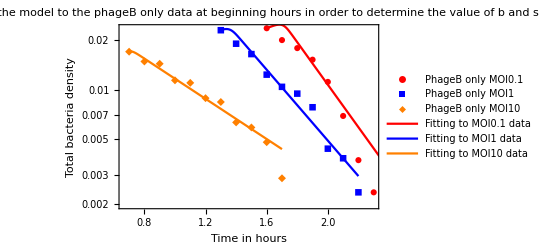

```mathematica
Show[PBg1,LogPlot[{PBfitModel1[t]},{t,1.6,2.4},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Fitting to MOI0.1 data"},LegendFunction->Framed],{0.5,0.3}]],LogPlot[{PBfitModel2[t]},{t,1.3,2.2},PlotStyle->Blue,PlotLegends->Placed[LineLegend[{"Fitting to MOI1 data"},LegendFunction->Framed],{0.5,0.2}]],LogPlot[{PBfitModel3[t]},{t,0.7,1.7},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Fitting to MOI10 data"},LegendFunction->Framed],{0.5,0.1}]],Frame->True,PlotTheme->"Scientific",ImageSize->Full,BaseStyle->{Bold,14},FrameStyle->{Bold,Black},PlotLabel->"Fitting the model to the phageB only data at beginning hours in order to determine the value of b and s",FrameLabel->{"Time in hours","Total bacteria density"}]
```

```mathematica
PH2[a_,k_,b_,h_,s_,p_,rb_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+rb*Br*(1-(B+Br)/k),-p*P+h*s*Bi,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+rb*Br*(1-(B+Br)/k)};
```

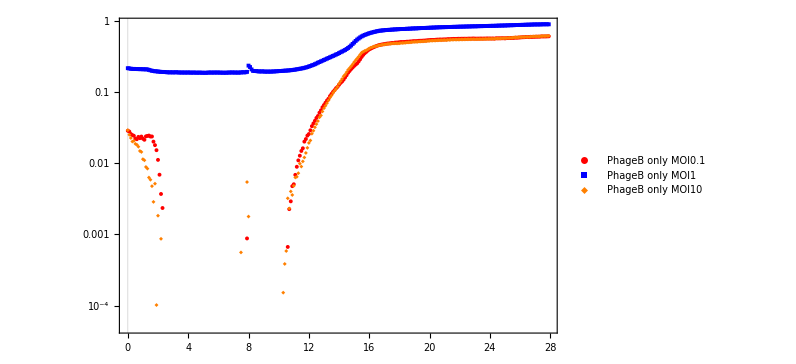

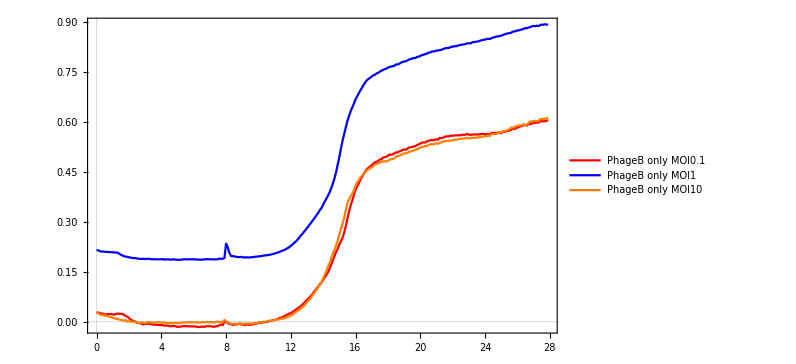

```mathematica
(* Models for different MOI, used to estimate a and rb *)
PH2[a_,k_,b_,h_,s_,p_,rb_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+rb*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+rb*Br*(1-(B+Br)/k)};
stateVar2={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar2[t]];
PBsol4=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rb]/.Thread[stateVar2->X[t]])},X[1.5]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,rb,B0,MOI}];
PBsol5=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rb]/.Thread[stateVar2->X[t]])},X[1.3]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,rb,B0,MOI}];
PBsolFinal=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rb]/.Thread[stateVar2->X[t]])},X[1.3]=={B0,0,0,B0*MOI,B0}},{B[t],Bi[t],Br[t],Bt[t]},{t,1.3,27.9},{a,k,b,h,s,p,rb,B0,MOI}];
PBsol6=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rb]/.Thread[stateVar2->X[t]])},X[0.7]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,rb,B0,MOI}];
PBmodel4[a_,k_,b_,h_,s_,p_,rb_,B0_,MOI_,t_]:=PBsol4[a,k,b,h,s,p,rb,B0,MOI][t]
PBmodel5[a_,k_,b_,h_,s_,p_,rb_,B0_,MOI_,t_]:=PBsol5[a,k,b,h,s,p,rb,B0,MOI][t]
PBmodel6[a_,k_,b_,h_,s_,p_,rb_,B0_,MOI_,t_]:=PBsol6[a,k,b,h,s,p,rb,B0,MOI][t]
afterB01=Select[phageBMOI01,1.5<=#[[1]]&];
afterB1=Select[phageBMOI1,1.3<=#[[1]]&];
afterB10=Select[phageBMOI10,0.7<=#[[1]]&];
PBMOI01INI=Select[phageBMOI01,1.5==#[[1]]&][[1,2]];
PBMOI1INI=Select[phageBMOI1,1.3==#[[1]]&][[1,2]];
PBMOI10INI=Select[phageBMOI10,0.7==#[[1]]&][[1,2]];
PBg2=ListLogPlot[{phageBMOI01,phageBMOI1,phageBMOI10},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageB only MOI0.1","PhageB only MOI1","PhageB only MOI10"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
PBg3=ListLinePlot[{phageBMOI01,phageBMOI1,phageBMOI10},PlotLegends->Placed[LineLegend[{"PhageB only MOI0.1","PhageB only MOI1","PhageB only MOI10"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
```

```mathematica
PBfitModel4=NonlinearModelFit[afterB01,{PBmodel4[a,k,277,100,2.273507296714341,0.09,rb,PBMOI01INI,0.1,t],0.008==a,k==0.605,0.85>rb>0.75},{{a,0.023},k,{rb,0.6783536287519775}},t];
```

ParametricNDSolveValue::ndsz: At t == 1.35183, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

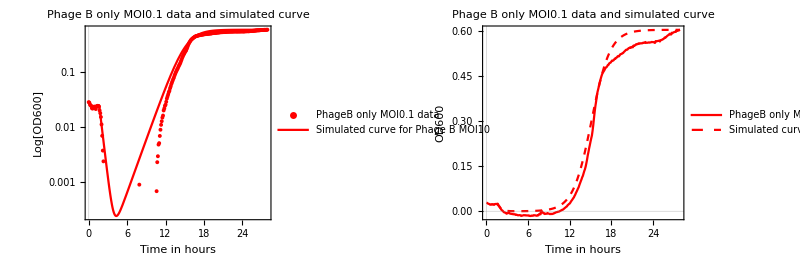

{a→0.008,k→0.605,rb→0.75}

```mathematica
PBg4=GraphicsGrid[{{Show[ListLogPlot[{phageBMOI01},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageB only MOI0.1 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[PBfitModel4[t],{t,1.5,27.9},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage B MOI10"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific",PlotRange->All],PlotLabel->"Phage B only MOI0.1 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"},PlotRange->All],Show[ListLinePlot[{phageBMOI01},PlotLegends->Placed[LineLegend[{"PhageB only MOI0.1 data"},LegendFunction->Framed],{0.75,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[PBfitModel4[t],{t,1.5,27.9},PlotStyle->{Dashed,Red},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage B MOI10"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage B only MOI0.1 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full]
PBfitModel4[[1,2]]
```

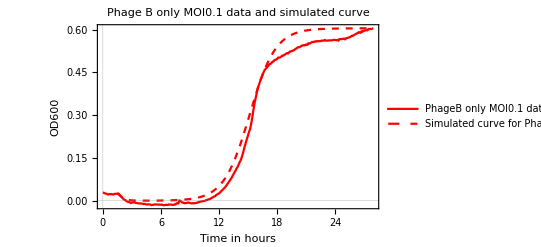

```mathematica
singlePhageG4=Show[ListLinePlot[{phageBMOI01},PlotLegends->Placed[LineLegend[{"PhageB only MOI0.1 data"},LegendFunction->Framed],{0.75,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[PBfitModel4[t],{t,1.5,27.9},PlotStyle->{Dashed,Red},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage B MOI10"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage B only MOI0.1 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
PBfitModel5=NonlinearModelFit[afterB1,{PBmodel5[a,k,460,100,0.25,0.09,rb,PBMOI1INI,1,t],a==0.005,k==0.893,rb==0.8},{{a,0.006},k,{rb,0.6783536287519775}},t];
```

ParametricNDSolveValue::ndsz: At t == 1.28974, step size is effectively zero; singularity or stiff system suspected.

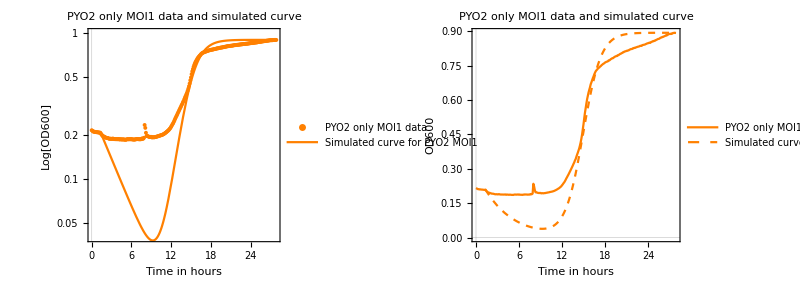

{a→0.005,k→0.893,rb→0.8}

```mathematica
PBg5=GraphicsGrid[{{Show[ListLogPlot[{phageBMOI1},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PYO2 only MOI1 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black},PlotRange->{{0,27.9},{0.04,1}}],LogPlot[PBfitModel5[t],{t,1.3,27.9},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Simulated curve for\nPYO2 MOI1"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific"],PlotLabel->"PYO2 only MOI1 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"}],Show[ListLinePlot[{phageBMOI1},PlotLegends->Placed[LineLegend[{"PYO2 only MOI1 data"},LegendFunction->Framed],{0.75,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[PBfitModel5[t],{t,1.3,27.9},PlotStyle->{Dashed,Orange},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPYO2 MOI1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"PYO2 only MOI1 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full,Frame->True,Alignment->Center,Spacings->0]
PBfitModel5[[1,2]]
```

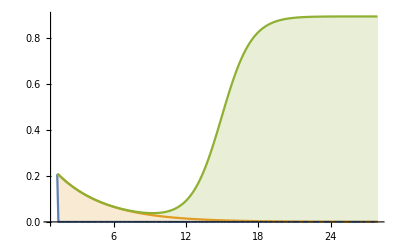

```mathematica
StackedListPlot[Transpose[Table[Map[{t,#}&,Evaluate[(PBsolFinal[a,k,460,100,0.25,0.09,rb,PBMOI1INI,1]/.PBfitModel5[[1,2]])[[1;;3]]]],{t,1.3,27.9,0.1}]]]
```

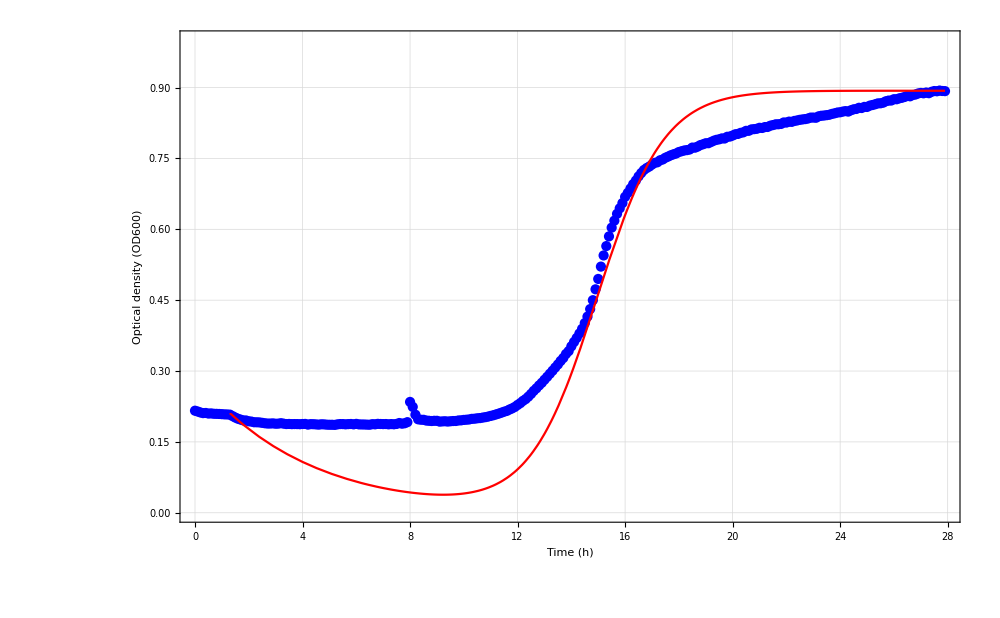

```mathematica
gf21=Show[ListPlot[{phageBMOI1},PlotLegends->Placed[PointLegend[{Directive[Blue,AbsolutePointSize[10]]},{"PYO2-only-MOI1 Bacteria data"}],{0.25,0.6}],Frame->True,PlotStyle->{Blue},PlotTheme->"Detailed",PlotStyle->{Blue},GridLines->Automatic,BaseStyle->{Bold,23},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Plot[PBfitModel5[t],{t,1.3,27.9},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated bacteria"}],{0.25,0.6}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->1000,PlotRange-> {{0,27.9},{0,1}}]
```

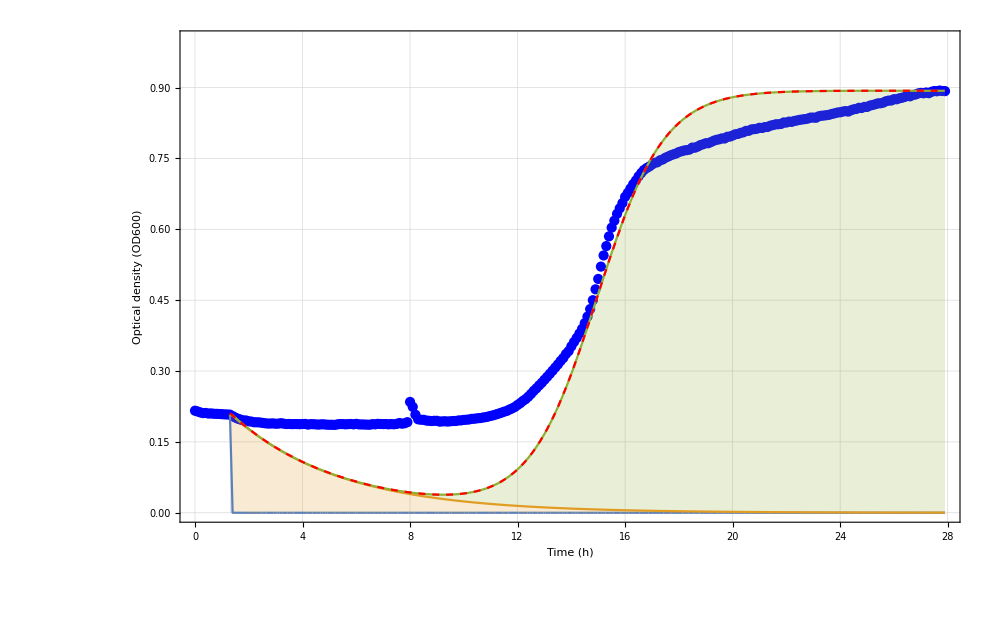

```mathematica
gf22=Show[ListPlot[{phageBMOI1},PlotLegends->Placed[PointLegend[{Directive[Blue,AbsolutePointSize[10]]},{"PYO2-only-MOI1 Bacteria data"}],{0.25,0.6}],Frame->True,PlotStyle->{Blue},PlotTheme->"Detailed",PlotStyle->{Blue},GridLines->Automatic,BaseStyle->{Bold,23},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],StackedListPlot[Transpose[Table[Map[{t,#}&,Evaluate[(PBsolFinal[a,k,460,100,0.25,0.09,rb,PBMOI1INI,1]/.PBfitModel5[[1,2]])[[1;;3]]]],{t,1.3,27.9,0.1}]],PlotLegends->Placed[SwatchLegend[{"Ancestral bacteria","Infected bacteria","Resistant bacteria"}],{0.25,0.6}],LabelStyle->{FontFamily->"Times"}],Plot[PBfitModel5[t],{t,1.3,27.9},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{"Simulated bacteria"}],{0.25,0.6}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->1000,PlotRange-> {{0,27.9},{0,1}}]
```

```mathematica
gf2=Grid[{{Style["B",FontFamily->"Times",FontSize->30]},{gf21},{gf22}}]
```

B
-Graphics-
-Graphics-

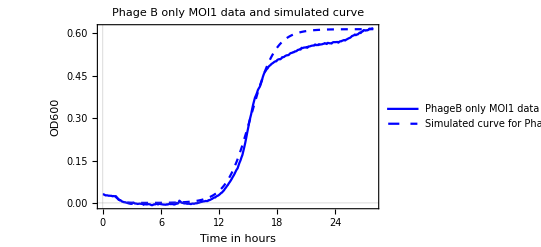

```mathematica
singlePhageG5=Show[ListLinePlot[{phageBMOI1},PlotLegends->Placed[LineLegend[{"PhageB only MOI1 data"},LegendFunction->Framed],{0.75,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Blue},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[PBfitModel5[t],{t,1.3,27.9},PlotStyle->{Dashed,Blue},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage B MOI1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage B only MOI1 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
PBfitModel6=NonlinearModelFit[afterB10,{PBmodel6[a,k,309.49773963509045,100,2.273507296714341,0.09,rb,PBMOI10INI,10,t],0.008==a,k==0.61,0.87>rb>0.86},{{a,0.023},k,{rb,0.6783536287519775}},t];
```

ParametricNDSolveValue::ndsz: At t == 0.654981, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

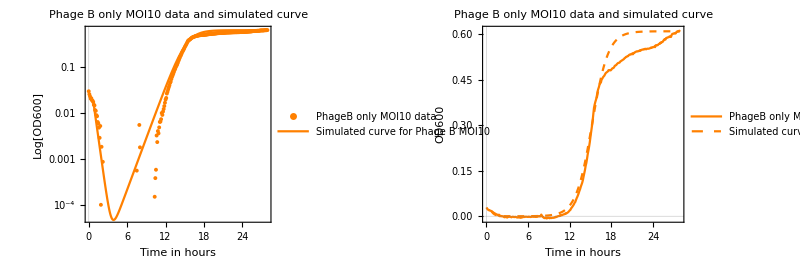

{a→0.008,k→0.61,rb→0.86}

```mathematica
PBg6=GraphicsGrid[{{Show[ListLogPlot[{phageBMOI10},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageB only MOI10 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[PBfitModel6[t],{t,0.7,27.9},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage B MOI10"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific"],PlotLabel->"Phage B only MOI10 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"}],Show[ListLinePlot[{phageBMOI10},PlotLegends->Placed[LineLegend[{"PhageB only MOI10 data"},LegendFunction->Framed],{0.75,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[PBfitModel6[t],{t,0.7,27.9},PlotStyle->{Dashed,Orange},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage B MOI10"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage B only MOI10 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full]
PBfitModel6[[1,2]]
```

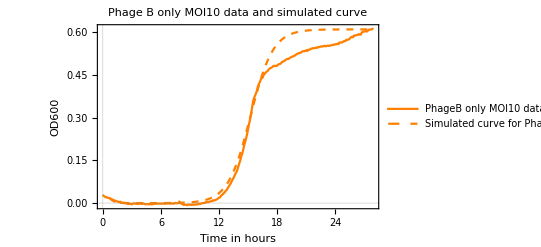

```mathematica
singlePhageG6=Show[ListLinePlot[{phageBMOI10},PlotLegends->Placed[LineLegend[{"PhageB only MOI10 data"},LegendFunction->Framed],{0.75,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[PBfitModel6[t],{t,0.7,27.9},PlotStyle->{Dashed,Orange},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage B MOI10"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage B only MOI10 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
(* a2 *)
```

```mathematica
Mean[{0.0030000521236647165,0.00446884398942673,0.00699999756671431}]
```

0.00482296

```mathematica
(* rb *)
```

```mathematica
Mean[{0.7500000146395103,0.7900009634864262,0.860000028893722}]
```

0.8

```mathematica
GraphicsGrid[{{PBg4},{PBg5},{PBg6}},Alignment->Center,Spacings->0,Frame->True,ImageSize->Full]
```

-Graphics-

## Estimate phage-C-specific parameter values

#### Fitting using data from phage C only experiment

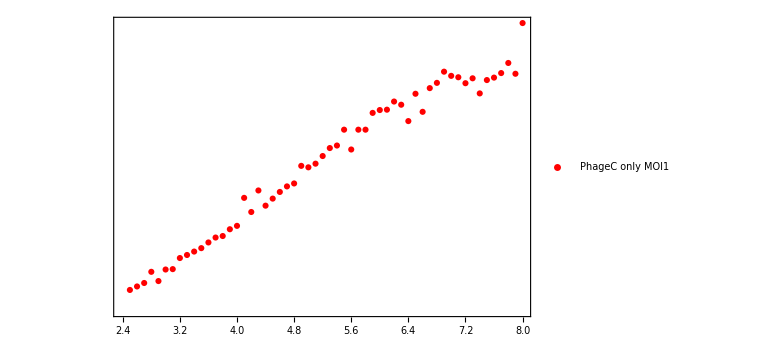

```mathematica
experimentData=Import["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\experimentNew.xlsx"];
TIME=Table[i,{i,0,27.9,0.1}];
phageCMOI01=Transpose[{TIME,experimentData[[7,1]]}];
phageCMOI1=Transpose[{TIME,experimentData[[8,1]]}];
phageCMOI10=Transpose[{TIME,experimentData[[9,1]]}];
beginC01=Select[phageCMOI01,0.5<=#[[1]]≤8&];
beginC1=Select[phageCMOI1,2.5<=#[[1]]≤8&];
beginC10=Select[phageCMOI10,1.3<=#[[1]]≤8&];PCg1=ListLogPlot[{beginC1},PlotMarkers->Automatic,PlotLegends->Placed[PointLegend[{"PhageC only MOI1"},LegendFunction->Framed],{0.2,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange}]
```

```mathematica
PH[a_,k_,b_,h_,s_,p_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+0.81*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+0.81*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
PCsol1=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[0.5]=={B0,0,0,B0*MOI,B0}},Bt,{t,0.5,8},{a,k,b,h,s,p,B0,MOI}];
PCsol2=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[2.5]=={B0,0,0,B0*MOI,B0}},Bt,{t,2.5,8},{a,k,b,h,s,p,B0,MOI}];
PCsol3=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[1.3]=={B0,0,0,B0*MOI,B0}},Bt,{t,1.3,8},{a,k,b,h,s,p,B0,MOI}];
PCmodel1[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=PCsol1[a,k,b,h,s,p,B0,MOI][t]
PCmodel2[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=PCsol2[a,k,b,h,s,p,B0,MOI][t]
PCmodel3[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=PCsol3[a,k,b,h,s,p,B0,MOI][t]
```

```mathematica
(* Initial bacteria values *)
PCMOI01INI=Select[phageCMOI01,0.5==#[[1]]&][[1,2]];
PCMOI1INI=Select[phageCMOI1,2.5==#[[1]]&][[1,2]];
PCMOI10INI=Select[phageCMOI10,1.3==#[[1]]&][[1,2]];
```

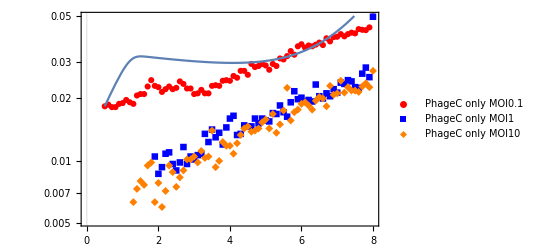

{b→129.998,s→0.0499989}

```mathematica
PCfitModel1=NonlinearModelFit[beginC01,{PCmodel1[0.008,1,b,200,s,0.09,PCMOI01INI,0.1,t],130>b>0,0<s<0.05},{b,s},t];
Show[PCg1,LogPlot[PCfitModel1[t],{t,0.5,8}]]
PCfitModel1[[1,2]]
```

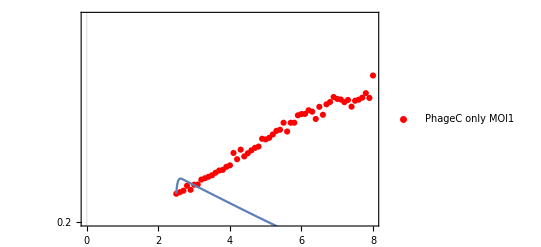

{b→460.,s→0.0200001}

```mathematica
PCfitModel2=NonlinearModelFit[beginC1,{PCmodel2[0.008,1,b,200,s,0.09,PCMOI1INI,1,t],b==460,0.02<s},{b,s},t];
Show[PCg1,LogPlot[PCfitModel2[t],{t,2.5,8},PlotRange->All],PlotRange->{{0,8},{0.2,0.25}//Log}]
PCfitModel2[[1,2]]
```

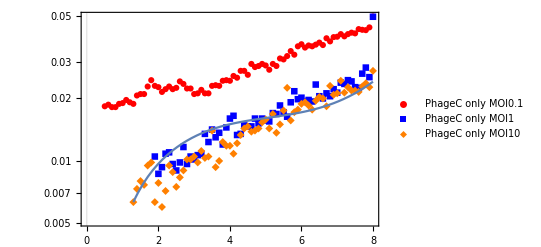

{b→20.1643,s→0.0100171}

```mathematica
PCfitModel3=NonlinearModelFit[beginC10,{PCmodel3[0.008,1,b,200,s,0.09,PCMOI10INI,10,t],100>b>20,0.01<s<3},{b,s},t];
Show[PCg1,LogPlot[PCfitModel3[t],{t,1.3,8}]]
PCfitModel3[[1,2]]
```

```mathematica
(* b *)
```

```mathematica
Mean[{279.2900341706015,276.221780102454,273.4717985074662}]
```

276.328

```mathematica
(* s *)
```

```mathematica
Mean[{1.0795990086697207,1.0427361634232657,1.0203150092631175}]
```

1.04755

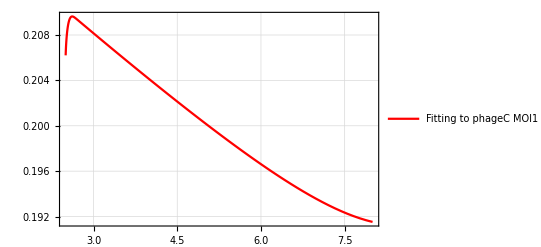

```mathematica
GphageCMOI1Early=Plot[{PCfitModel2[t]},{t,2.5,8},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Fitting to phageC MOI1 data"}],{0.2,0.1}],PlotTheme->"Detailed",ImageSize->Full,BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
```

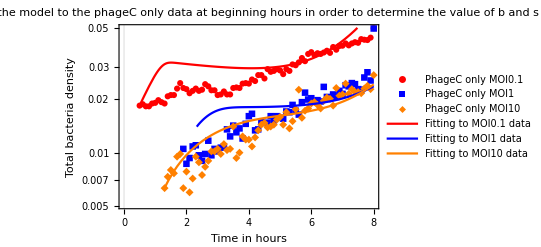

```mathematica
Show[PCg1,LogPlot[{PCfitModel1[t]},{t,0.5,8},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Fitting to MOI0.1 data"},LegendFunction->Framed],{0.5,0.3}]],LogPlot[{PCfitModel2[t]},{t,1.9,8},PlotStyle->Blue,PlotLegends->Placed[LineLegend[{"Fitting to MOI1 data"},LegendFunction->Framed],{0.5,0.2}]],LogPlot[{PCfitModel3[t]},{t,1.3,8},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Fitting to MOI10 data"},LegendFunction->Framed],{0.5,0.1}]],Frame->True,PlotTheme->"Scientific",ImageSize->Full,BaseStyle->{Bold,14},FrameStyle->{Bold,Black},PlotLabel->"Fitting the model to the phageC only data at beginning hours in order to determine the value of b and s",FrameLabel->{"Time in hours","Total bacteria density"}]
```

```mathematica
PH2[a_,k_,b_,h_,s_,p_,rc_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+rc*Br*(1-(B+Br)/k),-p*P+h*s*Bi,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+rc*Br*(1-(B+Br)/k)};
```

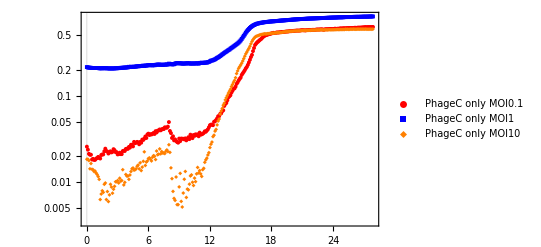

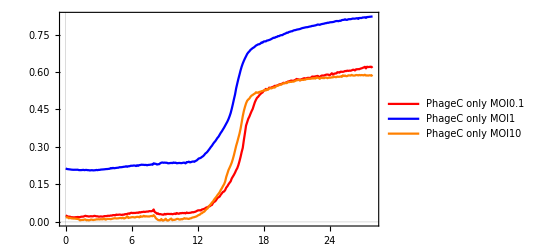

```mathematica
(* Models for different MOI, used to estimate a and rb *)
PH2[a_,k_,b_,h_,s_,p_,rc_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+rc*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+rc*Br*(1-(B+Br)/k)};
stateVar2={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar2[t]];
PCsol4=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rc]/.Thread[stateVar2->X[t]])},X[0]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,rc,B0,MOI}];
PCsol5=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rc]/.Thread[stateVar2->X[t]])},X[2.5]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,rc,B0,MOI}];
PCsol5New=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rc]/.Thread[stateVar2->X[t]])},X[2.5]=={B0,0,0,B0*MOI,B0}},{B,Bt},{t,0,27.9},{a,k,b,h,s,p,rc,B0,MOI}];
PCsolFinal=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rc]/.Thread[stateVar2->X[t]])},X[2.5]=={B0,0,0,B0*MOI,B0}},{B[t],Bi[t],Br[t],Bt[t]},{t,2.5,27.9},{a,k,b,h,s,p,rc,B0,MOI}];
PCsol6=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rc]/.Thread[stateVar2->X[t]])},X[0.8]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,rc,B0,MOI}];
PCmodel4[a_,k_,b_,h_,s_,p_,rc_,B0_,MOI_,t_]:=PCsol4[a,k,b,h,s,p,rc,B0,MOI][t]
PCmodel5[a_,k_,b_,h_,s_,p_,rc_,B0_,MOI_,t_]:=PCsol5[a,k,b,h,s,p,rc,B0,MOI][t]
PCmodel6[a_,k_,b_,h_,s_,p_,rc_,B0_,MOI_,t_]:=PCsol6[a,k,b,h,s,p,rc,B0,MOI][t]
afterC01=Select[phageCMOI01,0<=#[[1]]&];
afterC1=Select[phageCMOI1,2.5<=#[[1]]&];
afterC10=Select[phageCMOI10,0.8<=#[[1]]&];
PCMOI01INI=Select[phageCMOI01,0==#[[1]]&][[1,2]];
PCMOI1INI=Select[phageCMOI1,2.5==#[[1]]&][[1,2]];
PCMOI10INI=Select[phageCMOI10,0.8==#[[1]]&][[1,2]];
PCg2=ListLogPlot[{phageCMOI01,phageCMOI1,phageCMOI10},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageC only MOI0.1","PhageC only MOI1","PhageC only MOI10"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
PCg3=ListLinePlot[{phageCMOI01,phageCMOI1,phageCMOI10},PlotLegends->Placed[LineLegend[{"PhageC only MOI0.1","PhageC only MOI1","PhageC only MOI10"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
```

```mathematica
PCfitModel4=NonlinearModelFit[afterC01,{PCmodel4[a,k,276.3278709268406,100,1.0475500604520347,0.09,rc,PCMOI01INI,0.1,t],0.008==a,k==0.62,0.85>rc>0.8},{{a,0.023},k,{rc,0.6783536287519775}},t];
```

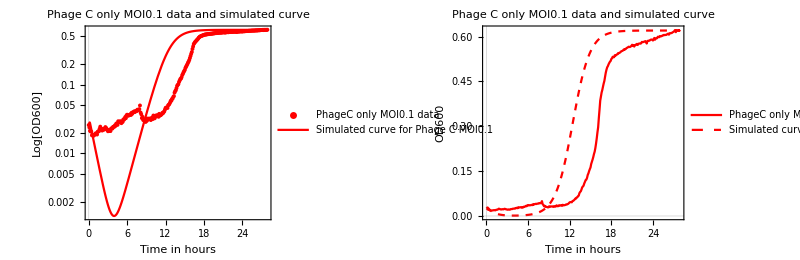

{a→0.008,k→0.62,rc→0.8}

```mathematica
PCg4=GraphicsGrid[{{Show[ListLogPlot[{phageCMOI01},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageC only MOI0.1 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[PCfitModel4[t],{t,0,27.9},PlotStyle->Red,PlotLegends->Placed[LineLegend[
{"Simulated curve for\nPhage C MOI0.1"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific"],PlotLabel->"Phage C only MOI0.1 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"},PlotRange->All],Show[ListLinePlot[{phageCMOI01},PlotLegends->Placed[LineLegend[{"PhageC only MOI0.1 data"},LegendFunction->Framed],{0.76,0.15}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[PCfitModel4[t],{t,0,27.9},PlotStyle->{Dashed,Red},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage C MOI0.1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage C only MOI0.1 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full]
PCfitModel4[[1,2]]
```

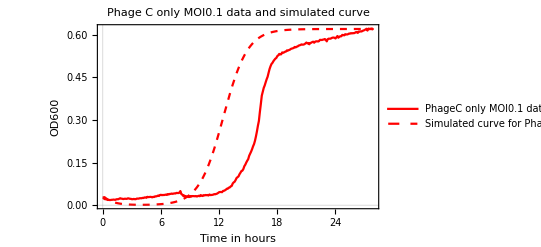

```mathematica
singlePhageG7=Show[ListLinePlot[{phageCMOI01},PlotLegends->Placed[LineLegend[{"PhageC only MOI0.1 data"},LegendFunction->Framed],{0.76,0.15}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[PCfitModel4[t],{t,0,27.9},PlotStyle->{Dashed,Red},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage C MOI0.1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage C only MOI0.1 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
PCfitModel5=NonlinearModelFit[afterC1,{PCmodel5[a,k,460,200,0.02,0.09,rc,PCMOI1INI,1,t],0.005==a,k==0.695,rc==0.81},{{a,0.023},k,{rc,0.6783536287519775}},t];
```

ParametricNDSolveValue::ndsz: At t == 2.48949, step size is effectively zero; singularity or stiff system suspected.

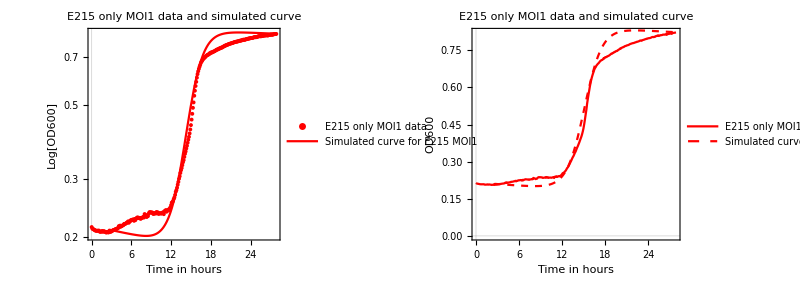

{a→0.0045,k→0.66,rc→0.81}

```mathematica
PCg5=GraphicsGrid[{{Show[ListLogPlot[{phageCMOI1},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"E215 only MOI1 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[PCfitModel5[t],{t,2.5,27.9},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Simulated curve for\nE215 MOI1"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific"],PlotLabel->"E215 only MOI1 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"},PlotRange->All],Show[ListLinePlot[{phageCMOI1},PlotLegends->Placed[LineLegend[{"E215 only MOI1 data"},LegendFunction->Framed],{0.77,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[PCfitModel5[t],{t,2.5,27.9},PlotStyle->{Dashed,Red},PlotLegends->Placed[LineLegend[{"Simulated curve for\nE215 MOI1"},LegendFunction->Framed],{0.26,0.85}],PlotTheme->"Scientific"],PlotLabel->"E215 only MOI1 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full,Frame->True,Alignment->Center,Spacings->0]
PCfitModel5[[1,2]]
```

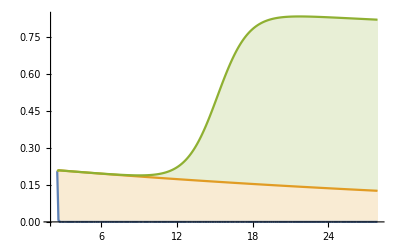

```mathematica
StackedListPlot[Transpose[Table[Map[{t,#}&,Evaluate[(PCsolFinal[a,k,460,200,0.02,0.09,rc,PCMOI1INI,1]/.PCfitModel5[[1,2]])[[1;;3]]]],{t,2.5,27.9,0.1}]]]
```

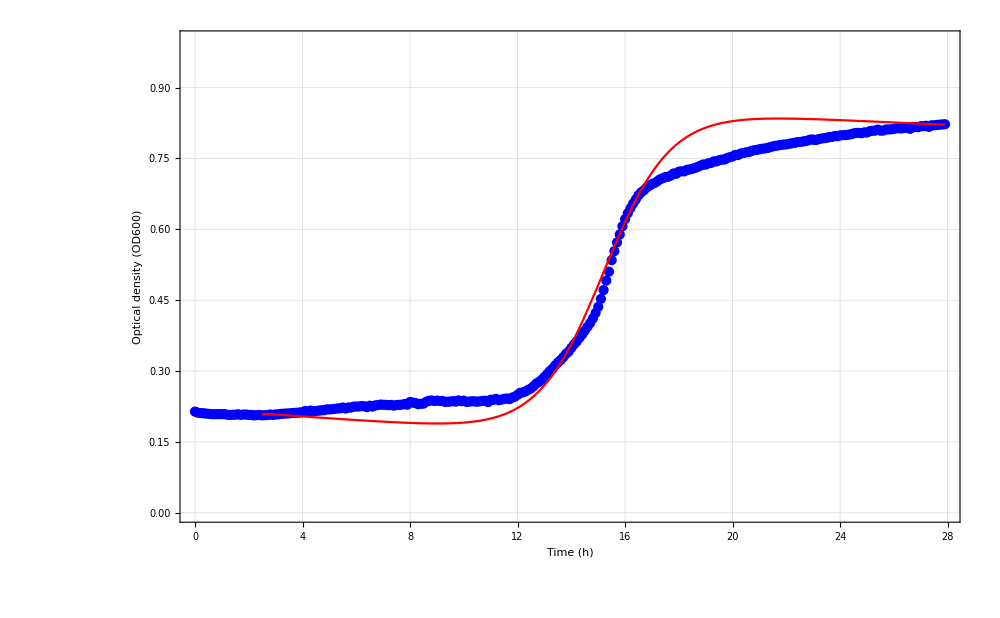

```mathematica
gf31=Show[ListPlot[{phageCMOI1},PlotLegends->Placed[PointLegend[{Directive[Blue,AbsolutePointSize[10]]},{"E215-only-MOI1 Bacteria data"}],{0.25,0.6}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue},GridLines->Automatic,BaseStyle->{Bold,23},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Plot[PCfitModel5[t],{t,2.5,27.9},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated bacteria"}],{0.25,0.6}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->1000,PlotRange-> {{0,27.9},{0,1}}]
```

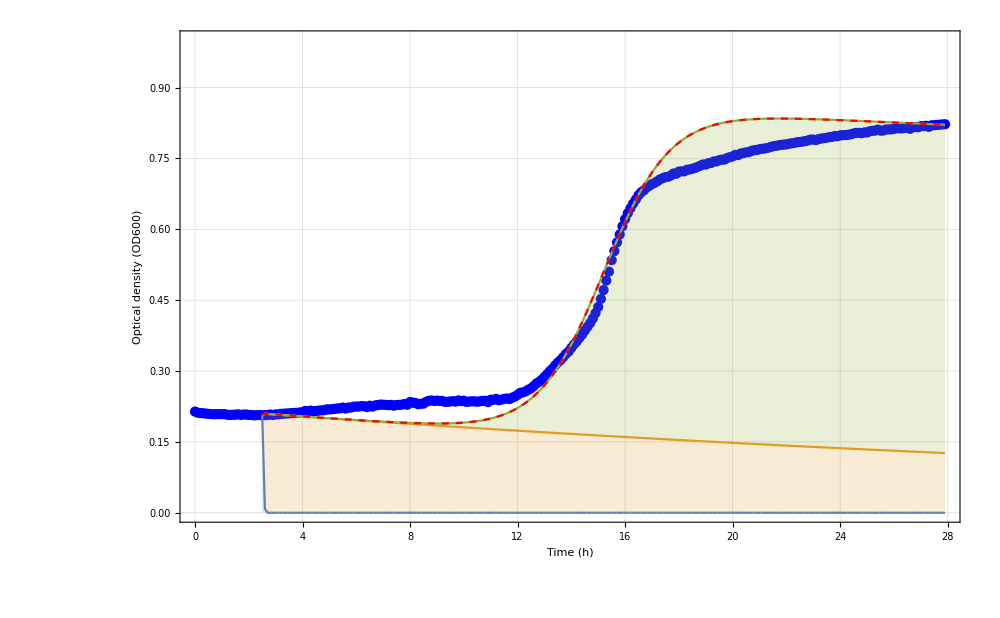

```mathematica
gf32=Show[ListPlot[{phageCMOI1},PlotLegends->Placed[PointLegend[{Directive[Blue,AbsolutePointSize[10]]},{"E215-only-MOI1 Bacteria data"}],{0.25,0.6}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue},GridLines->Automatic,BaseStyle->{Bold,23},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],StackedListPlot[Transpose[Table[Map[{t,#}&,Evaluate[(PCsolFinal[a,k,460,200,0.02,0.09,rc,PCMOI1INI,1]/.PCfitModel5[[1,2]])[[1;;3]]]],{t,2.5,27.9,0.1}]],PlotLegends->Placed[SwatchLegend[{"Ancestral bacteria","Infected bacteria","Resistant bacteria"}],{0.25,0.6}],LabelStyle->{FontFamily->"Times"}],Plot[PCfitModel5[t],{t,2.5,27.9},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{"Simulated bacteria"}],{0.25,0.6}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->1000,PlotRange-> {{0,27.9},{0,1}}]
```

```mathematica
gf3=Grid[{{Style["C",FontFamily->"Times",FontSize->30]},{gf31},{gf32}}]
```

C
-Graphics-
-Graphics-

```mathematica
Through[PCsol5New[0.008,0.88,460,200,0.001,0.09,0.81,PCMOI1INI,1][20]]
```

{-1.20298×10^-15,1.05424}

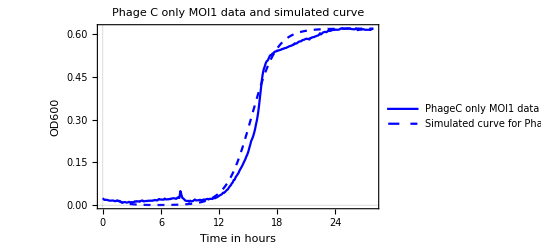

```mathematica
singlePhageG8=Show[ListLinePlot[{phageCMOI1},PlotLegends->Placed[LineLegend[{"PhageC only MOI1 data"},LegendFunction->Framed],{0.77,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Blue},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[PCfitModel5[t],{t,1.4,27.9},PlotStyle->{Dashed,Blue},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage C MOI1"},LegendFunction->Framed],{0.26,0.85}],PlotTheme->"Scientific"],PlotLabel->"Phage C only MOI1 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
PCfitModel6=NonlinearModelFit[afterC10,{PCmodel6[a,k,276.3278709268406,100,1.0475500604520347,0.09,rc,PCMOI10INI,10,t],0.008==a,k==0.59,0.87>rc>0.86},{{a,0.023},k,{rc,0.6783536287519775}},t];
```

ParametricNDSolveValue::ndsz: At t == 0.728523, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

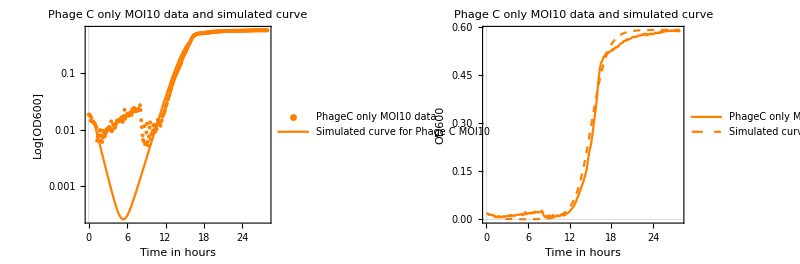

{a→0.008,k→0.59,rc→0.86}

```mathematica
PCg6=GraphicsGrid[{{Show[ListLogPlot[{phageCMOI10},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageC only MOI10 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[PCfitModel6[t],{t,0.8,27.9},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage C MOI10"},LegendFunction->Framed],{0.7,0.5}],PlotTheme->"Scientific"],PlotLabel->"Phage C only MOI10 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"},PlotRange->All],Show[ListLinePlot[{phageCMOI10},PlotLegends->Placed[LineLegend[{"PhageC only MOI10 data"},LegendFunction->Framed],{0.77,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[PCfitModel6[t],{t,0.8,27.9},PlotStyle->{Dashed,Orange},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage C MOI10"},LegendFunction->Framed],{0.26,0.85}],PlotTheme->"Scientific"],PlotLabel->"Phage C only MOI10 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full]
PCfitModel6[[1,2]]
```

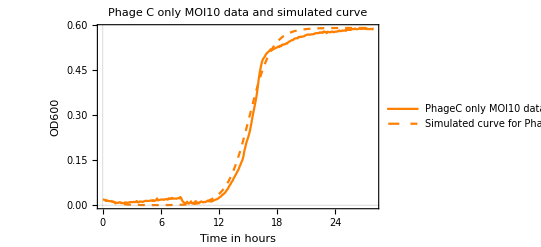

```mathematica
singlePhageG9=Show[ListLinePlot[{phageCMOI10},PlotLegends->Placed[LineLegend[{"PhageC only MOI10 data"},LegendFunction->Framed],{0.77,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[PCfitModel6[t],{t,0.8,27.9},PlotStyle->{Dashed,Orange},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage C MOI10"},LegendFunction->Framed],{0.26,0.85}],PlotTheme->"Scientific"],PlotLabel->"Phage C only MOI10 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
Mean[{0.8,0.7800000138400899,0.8600000337190107}]
```

0.813333

```mathematica
GraphicsGrid[{{PCg4},{PCg5},{PCg6}},Alignment->Center,Spacings->0,Frame->True,ImageSize->Full]
```

-Graphics-

-Graphics-

-Graphics-

## Summary

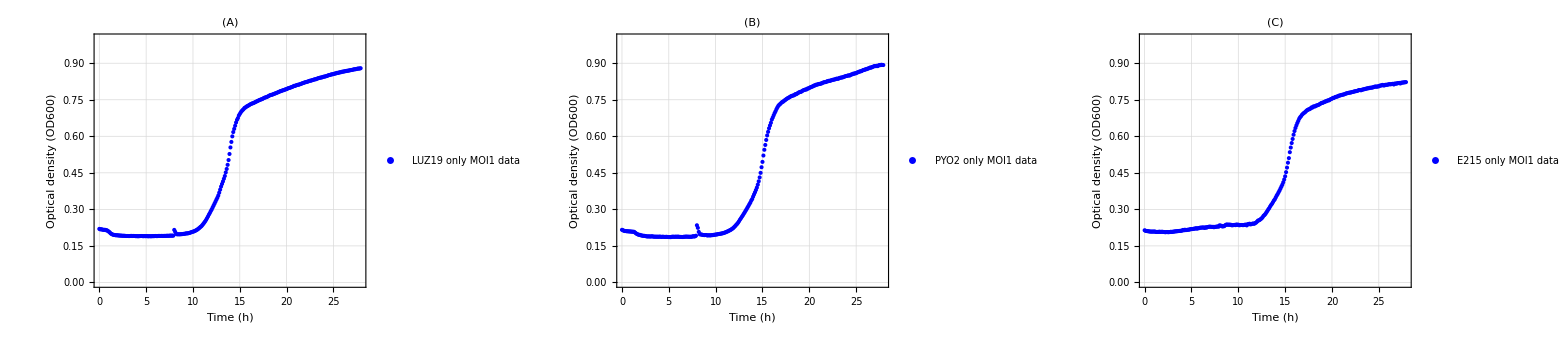

```mathematica
GraphicsGrid[{{ListPlot[{phageAMOI1},PlotLegends->Placed[LineLegend[{"LUZ19 only MOI1 data"}],{0.25,0.6}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,14},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->Full,PlotRange-> {{0,27.9},{0,1}},PlotLabel->"(A)"],ListPlot[{phageBMOI1},PlotLegends->Placed[LineLegend[{"PYO2 only MOI1 data"}],{0.25,0.6}],Frame->True,PlotStyle->{Blue},PlotTheme->"Detailed",PlotStyle->{Blue},GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->Full,PlotRange-> {{0,27.9},{0,1}},PlotLabel->"(B)"],ListPlot[{phageCMOI1},PlotLegends->Placed[LineLegend[{"E215 only MOI1 data"}],{0.25,0.6}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue},GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->Full,PlotRange-> {{0,27.9},{0,1}},PlotLabel->"(C)"]}},Alignment->Center,Spacings->0]
```

## Different phage lysis rates

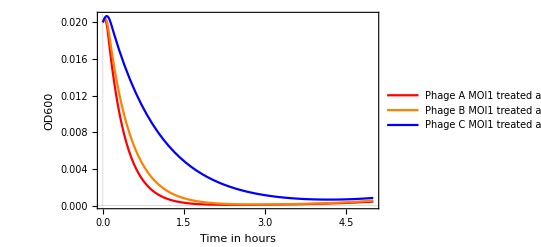

```mathematica
Module[{PH,stateVar,X,solution},
PH[a_,k_,b_,h_,s_,p_,r_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+r*Br*(1-(B+Br)/k),-p*P+h*s*Bi,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+r*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
solution=ParametricNDSolveValue[{{X'[t]==(PH[0.008,0.6,277,100,s,0.09,r]/.Thread[stateVar->X[t]])},X[0]=={B0,0,0,B0,B0}},Bt[t],{t,0,27.9},{s,r,B0}];
Plot[{solution[2.98,0.77,0.02],solution[2.3,0.8,0.02],solution[1.05,0.81,0.02]},{t,0,5},PlotTheme->"Scientific",PlotStyle->{Red,Orange,Blue},BaseStyle->{Bold,14},ImageSize->Full,PlotRange->All,PlotLegends->Placed[LineLegend[{"Phage A MOI1 treated at hour 0","Phage B MOI1 treated at hour 0","Phage C MOI1 treated at hour 0"},LegendFunction->Framed],{0.5,0.8}],FrameLabel->{"Time in hours","OD600"}]
]
```

## Single Phage Summary

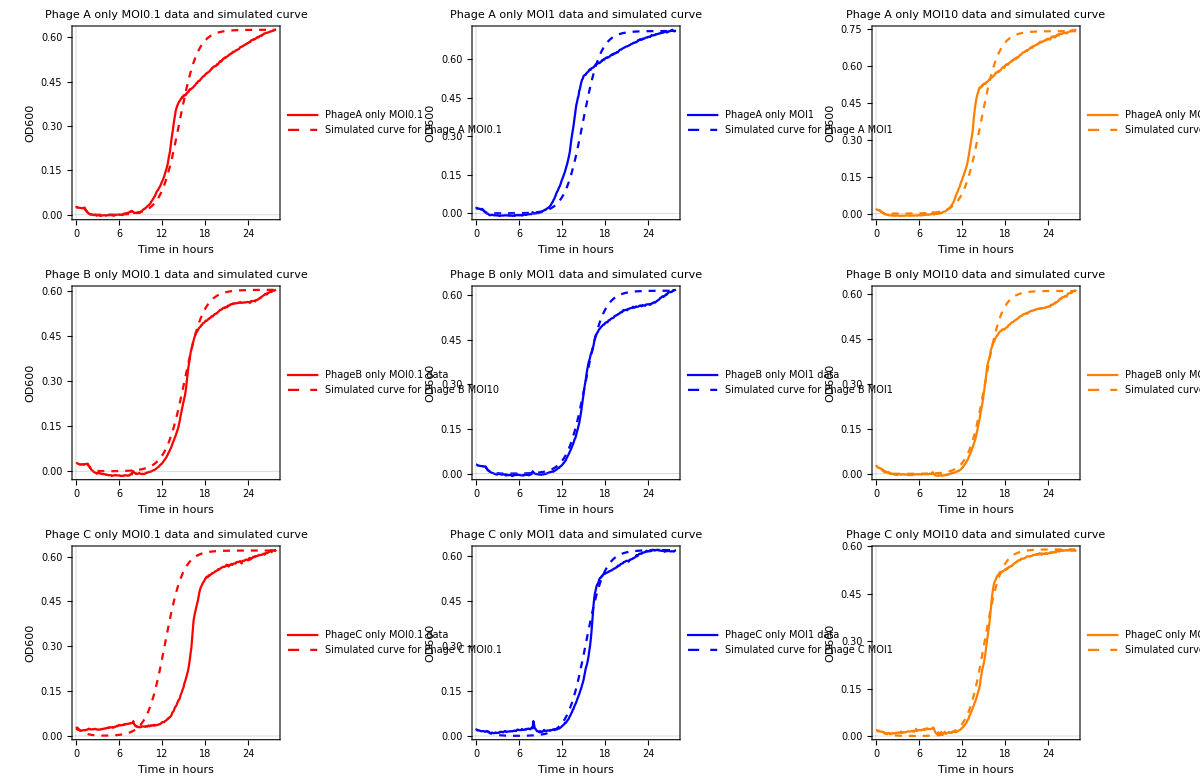

```mathematica
GraphicsGrid[{{singlePhageG1,singlePhageG2,singlePhageG3},{singlePhageG4,singlePhageG5,singlePhageG6},{singlePhageG7,singlePhageG8,singlePhageG9}},ImageSize->Full,Spacings->0,Frame->True,Alignment->Center]
```

## MOI1

```mathematica
GraphicsGrid[{{g5},{PBg5},{PCg5}},ImageSize->Full,Alignment->Center,Spacings->0,Frame->True]
```

-Graphics-

```mathematica
A=1
B=2
```

1

2

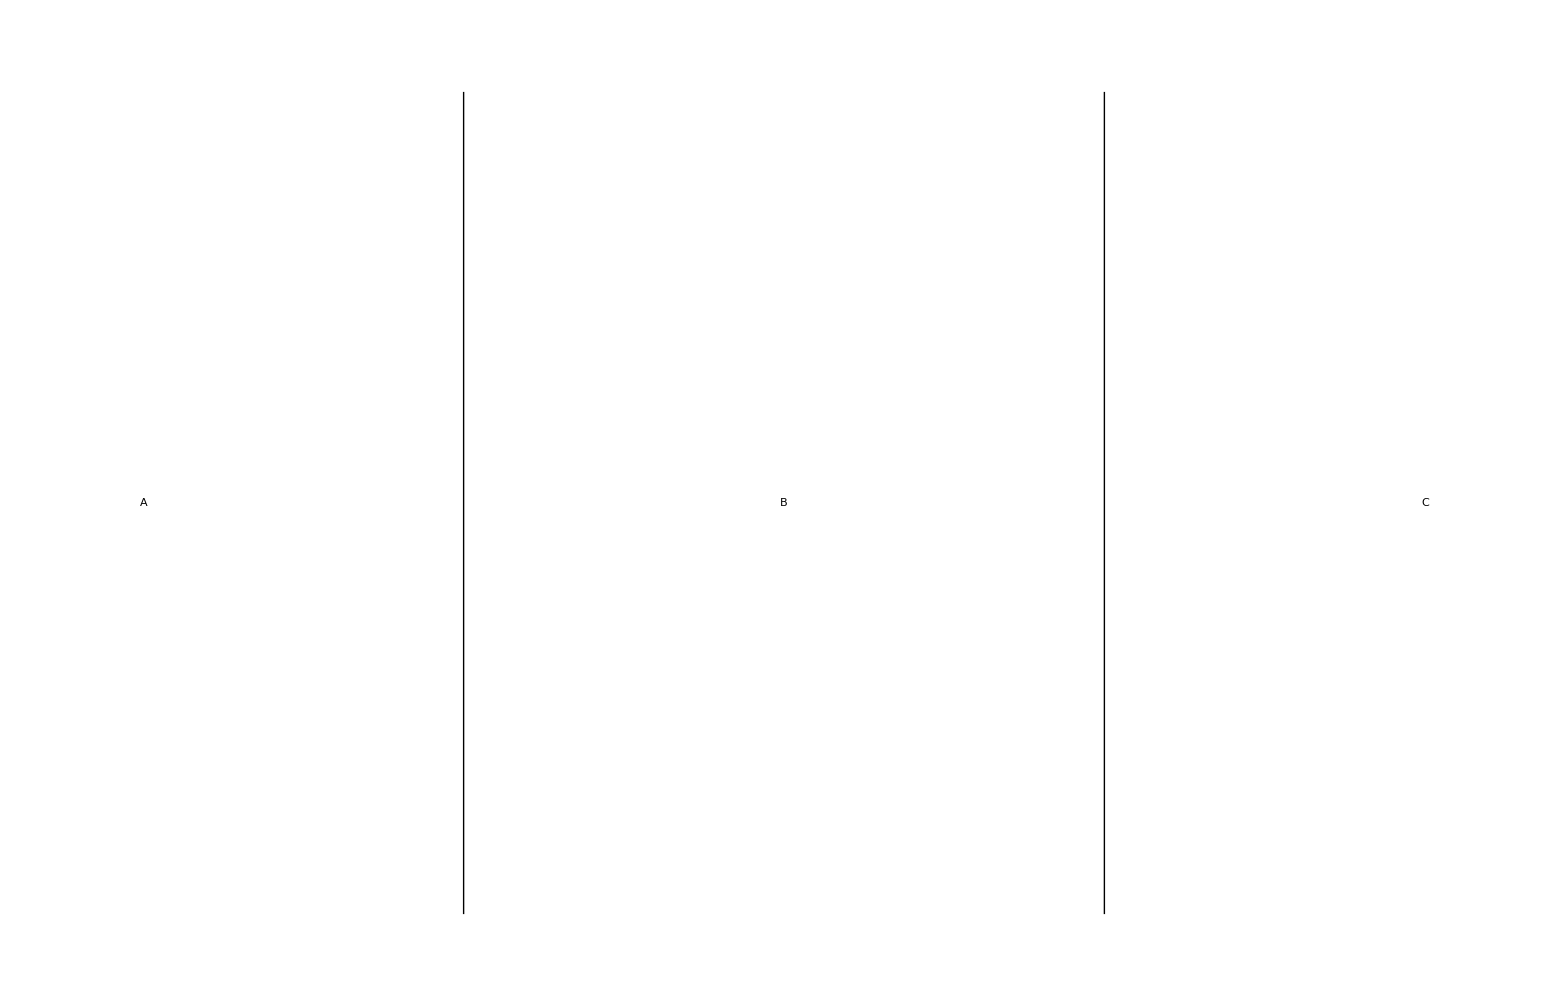

```mathematica
GraphicsGrid[{{gf1,gf2,gf3}},Alignment->Center,ImageSize->3200,Dividers->{{False,True,True,False},False}]
```

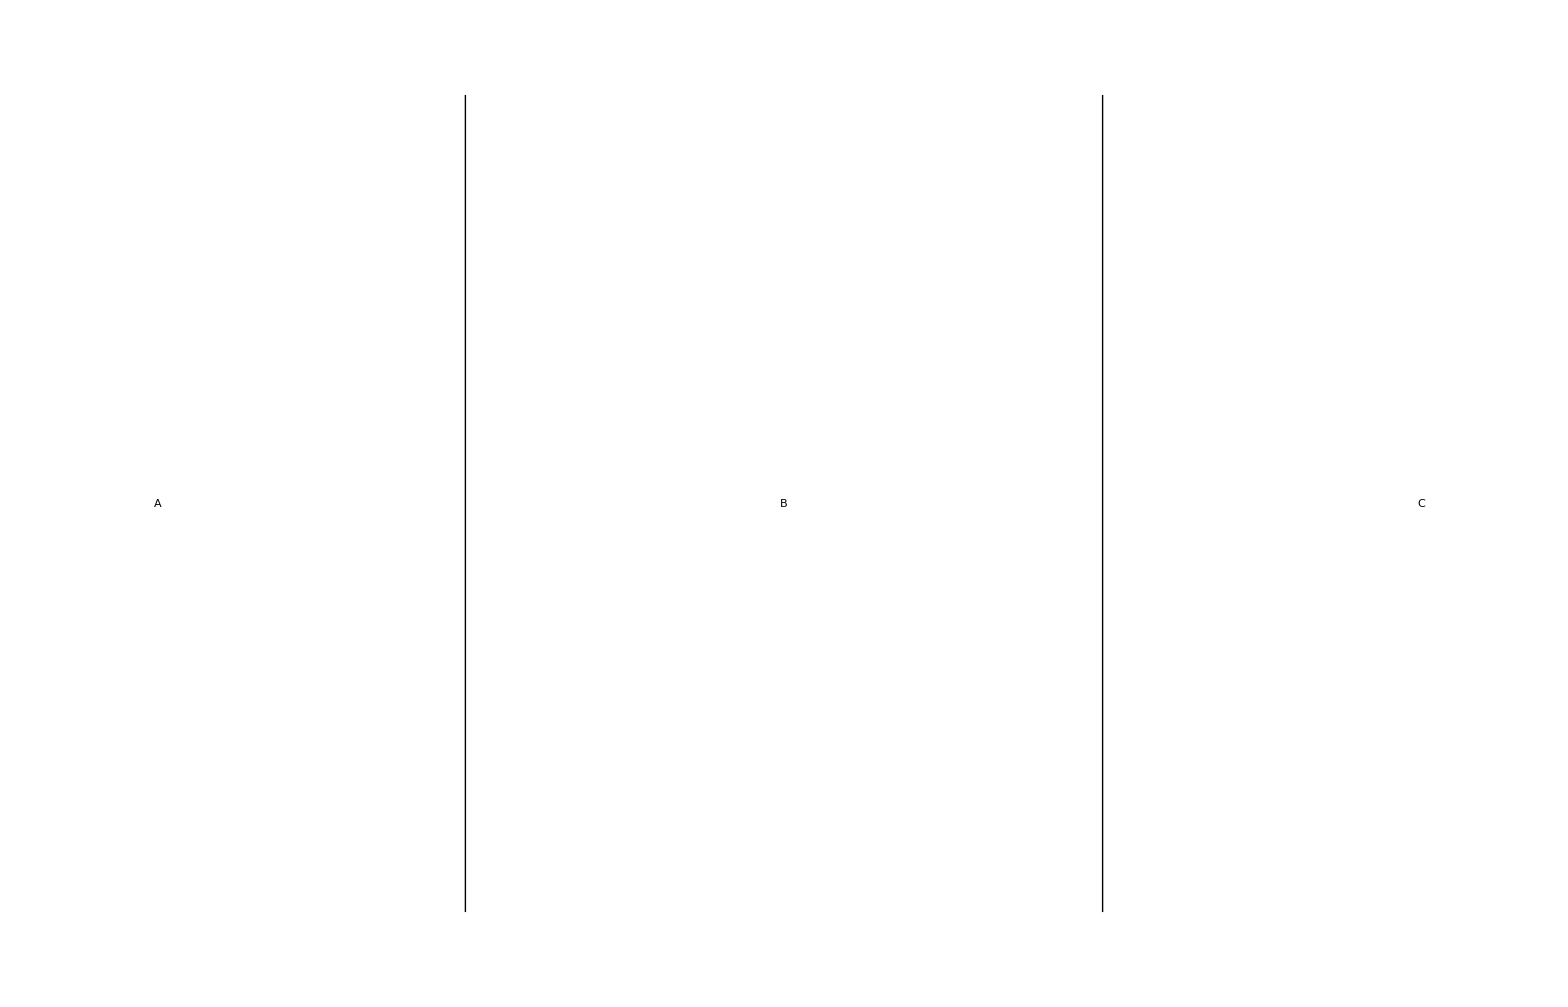

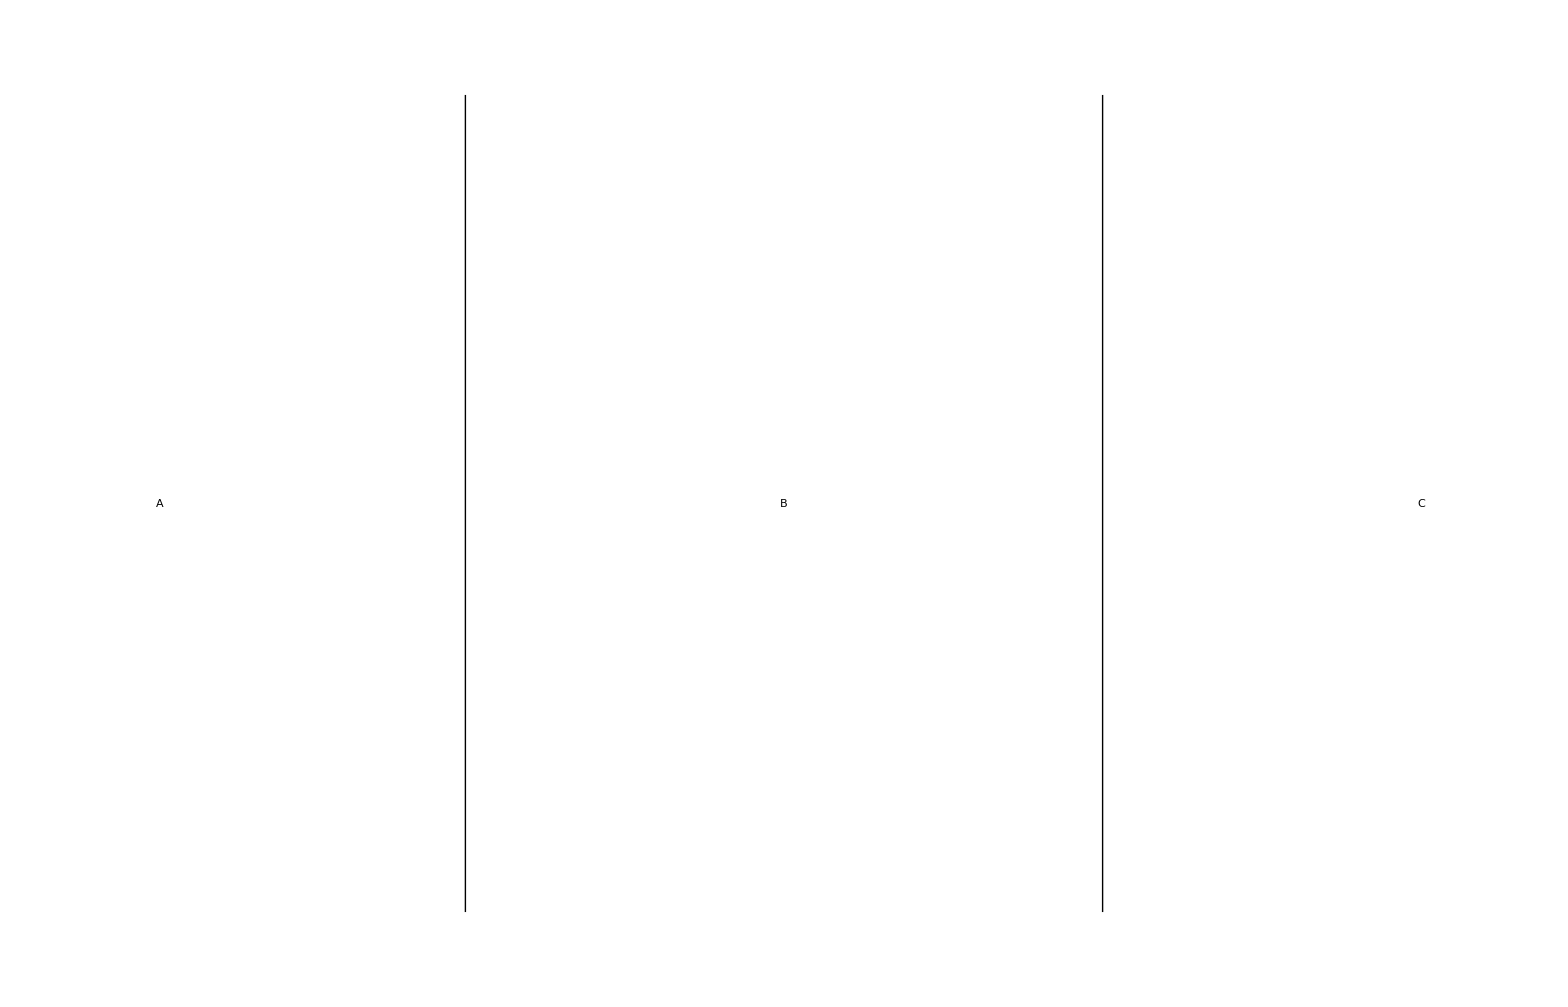

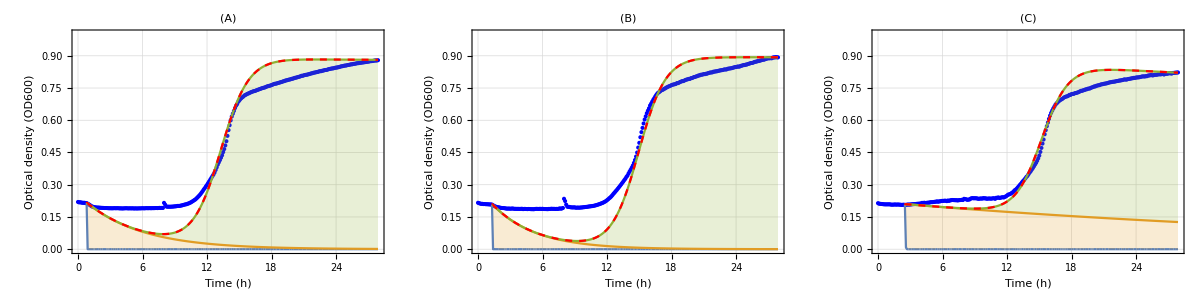

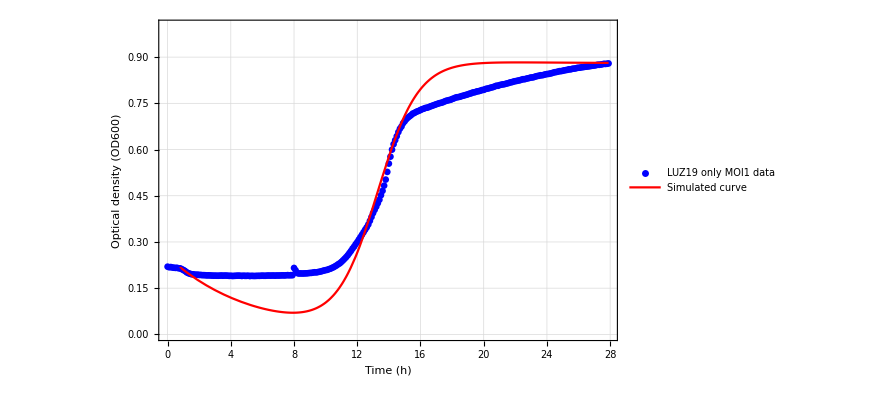
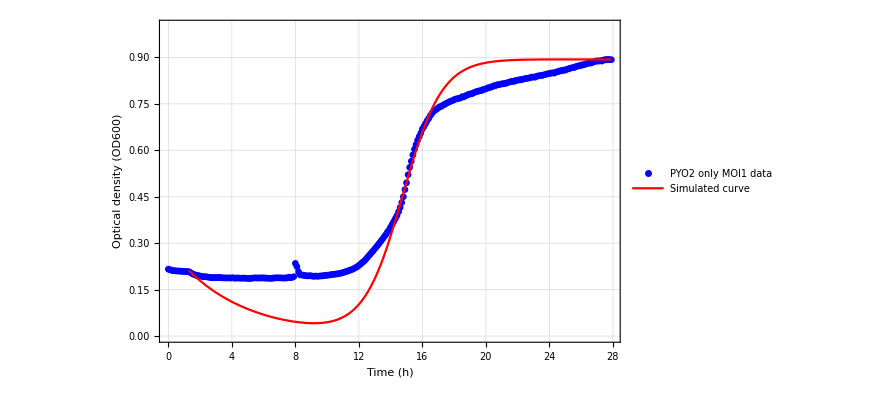
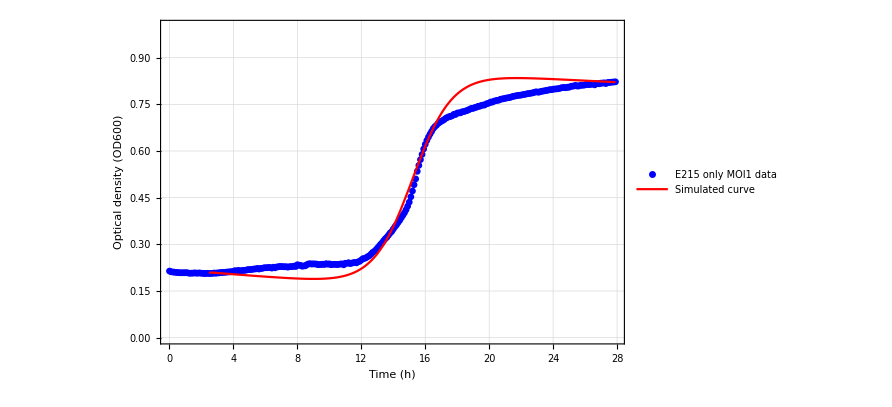
```mathematica
{{(A), (B), (C)}, {-Graphics-, -Graphics-, -Graphics-}}
```

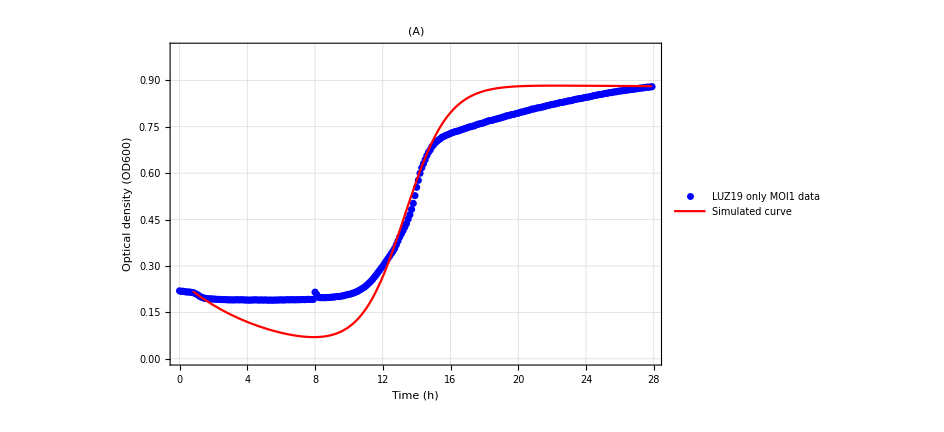

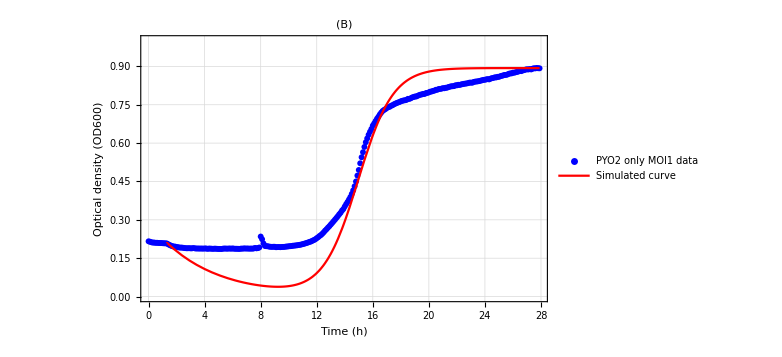

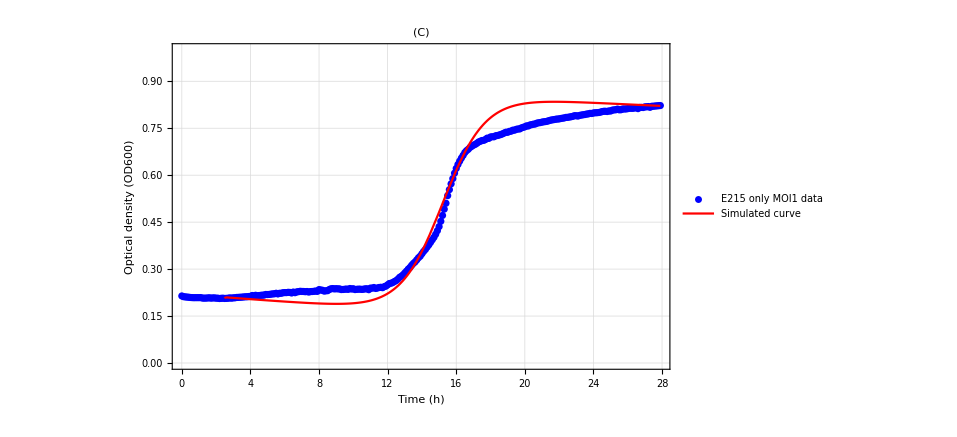

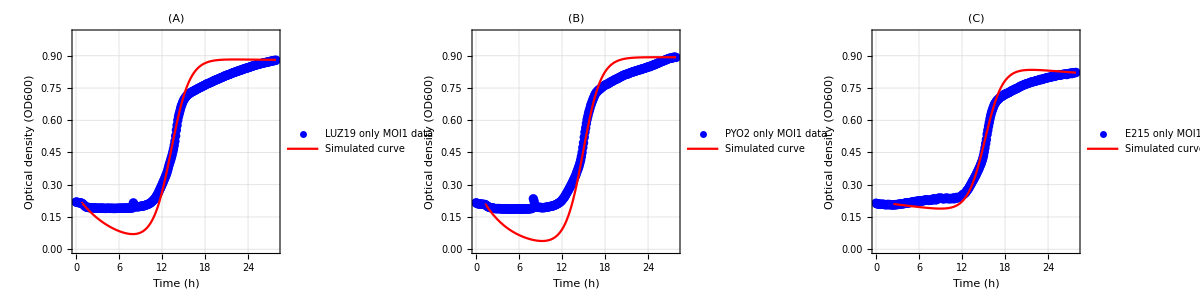

## MOI1 early

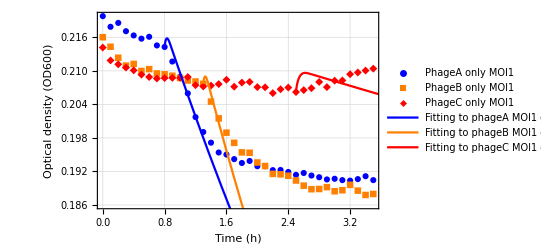

```mathematica
Show[ListPlot[{Select[phageAMOI1,0<=#[[1]]≤3.5&],Select[phageBMOI1,0<=#[[1]]≤3.5&],Select[phageCMOI1,0<=#[[1]]≤3.5&]},PlotMarkers->Automatic,PlotLegends->Placed[PointLegend[{"PhageA only MOI1","PhageB only MOI1","PhageC only MOI1"}],{0.2,0.5}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue,Orange,Red},BaseStyle->{Bold,14},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->All],GphageAMOI1Early,GphageBMOI1Early,GphageCMOI1Early,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"}]
```

## Delayed differential equation

```mathematica
CFU[x_]:=57115528.37x+9785470.84
```

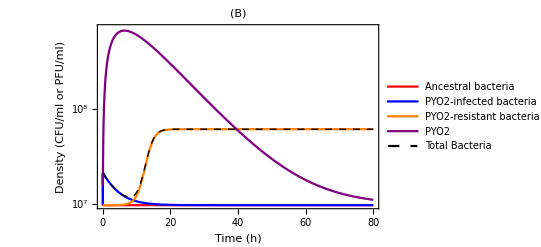

```mathematica
PH2[k_,a_]={0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.005*B+a*Br,-0.25*Bi+460*B*P,0.005*B+0.8*Br*(1-(B+Br)/k)-a*Br,-0.09*P+100*0.25*Bi-460*B*P,0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.005*B-0.25*Bi+460*B*P+0.005*B+0.8*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
parameterValues={k->0.9,a->0};
sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
Plot[Evaluate[sol],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Ancestral bacteria","PYO2-infected bacteria","PYO2-resistant bacteria","PYO2","Total Bacteria"}],{0.74,0.73}],PlotTheme->"Detailed",FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Blue},{Orange},{Purple},{Black,Dashed,Thick}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(B)"]
```

```mathematica
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
PHdelayearly[rn_,a_,k_,b_,h_,p_,rc_]={rn*B*(1-(B+Br)/k)-b*B*P-a*B,b*B*P-Bi*0.05,a*B+rc*Br*(1-(B+Br)/k),-p*P-b*B*P,rn*B*(1-(B+Br)/k)-b*B*P-a*B+b*B*P-Bi*0.05+a*B+rc*Br*(1-(B+Br)/k)}/.Thread[stateVar->X[t]];
X'[t]==PHdelay[rn,a,k,b,h,p,rc]
PHdelay[rn_,a_,k_,b_,h_,p_,rc_]={rn*B*(1-(B+Br)/k)-b*B*P-a*B,-delay+b*B*P-Bi*0,a*B+rc*Br*(1-(B+Br)/k),-p*P+h*delay-b*B*P,rn*B*(1-(B+Br)/k)-b*B*P-a*B-delay+b*B*P-Bi*0+a*B+rc*Br*(1-(B+Br)/k)}/.Thread[stateVar->X[t]]/.{delay->b*B[t-τ]*P[t-τ]};
X'[t]==PHdelay[rn,a,k,b,h,p,rc]
soldelay=ParametricNDSolveValue[{X'[t]==PHdelay[rn,a,k,b,h,p,rc],X[t/;t<=-1]=={0,0,0,0,0},WhenEvent[t==0,{B[t]->B0,P[t]->B0*MOI,Bt[t]->B0}]},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,-1,100},{rn,a,k,b,h,τ,p,rc,B0,MOI}]
```

{B'[t],Bi'[t],Br'[t],P'[t],Bt'[t]}==PHdelay[rn,a,k,b,h,p,rc]

{B'[t],Bi'[t],Br'[t],P'[t],Bt'[t]}=={-a B[t]+rn B[t] (1-(B[t]+Br[t])/k)-b B[t] P[t],b B[t] P[t]-b B[t-τ] P[t-τ],a B[t]+rc Br[t] (1-(B[t]+Br[t])/k),-p P[t]-b B[t] P[t]+b h B[t-τ] P[t-τ],rn B[t] (1-(B[t]+Br[t])/k)+rc Br[t] (1-(B[t]+Br[t])/k)-b B[t-τ] P[t-τ]}

ParametricFunction[<>]

ParametricFunction[<>]

```mathematica
soldelay=ParametricNDSolveValue[{X'[t]==PHdelay[rn,a,k,b,h,p,rc],X[t/;t<=-1]=={0,0,0,0,0},WhenEvent[t==0,{B[t]->B0,P[t]->B0*MOI,Bt[t]->B0}]},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,-1,100},{rn,a,k,b,h,τ,p,rc,B0,MOI}]
```

ParametricFunction[<>]

```mathematica
soldelay[0.8772547720626924,0.005,0.9,460,100,26/60,0.09,0.8,0.2,1]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
X'[t]==PHdelayearly[rn,a,k,b,h,p,rc]
```

{B'[t],Bi'[t],Br'[t],P'[t],Bt'[t]}=={-a B[t]+rn B[t] (1-(B[t]+Br[t])/k)-b B[t] P[t],b B[t] P[t],a B[t]+rc Br[t] (1-(B[t]+Br[t])/k),-p P[t]-b B[t] P[t],rn B[t] (1-(B[t]+Br[t])/k)+rc Br[t] (1-(B[t]+Br[t])/k)}

```mathematica
soldelay=ParametricNDSolveValue[{X'[t]==PHdelay[rn,a,k,b,h,p,rc],X[t/;t<=0]=={0,0,0,0,0},WhenEvent[t==0,B[t]->B0;Bt[t]->B0;P[t]->B0*MOI]},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,100},{rn,a,k,b,h,τ,p,rc,B0,MOI}]
```

```mathematica
26/60//N
```

0.433333

```mathematica
1/0.25
```

4.

```mathematica
Evaluate[soldelay[0.8772547720626924,0.005,0.9,460,100,26/60,0.09,0.8,0.2,1]]/.t->0.5
```

{9.78547×10^6,1.17841×10^7,9.78921×10^6,9.93024×10^8,1.17879×10^7}

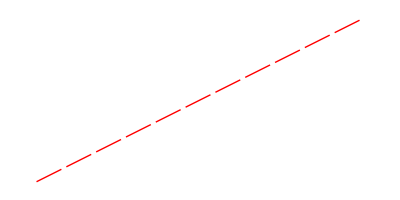

Dashing[{0.05,0.01}]

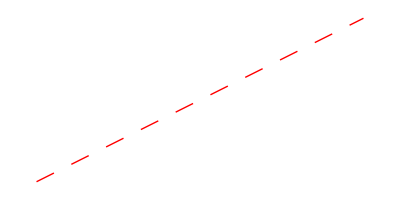

Dashing[Large]

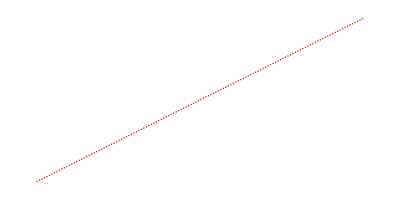

{Dashing[{0.002,0.003}],Thickness[Large]}

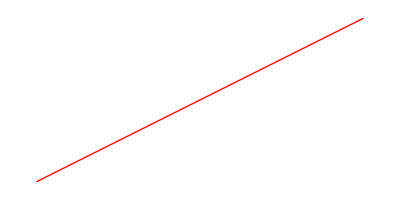

Dashing[None]

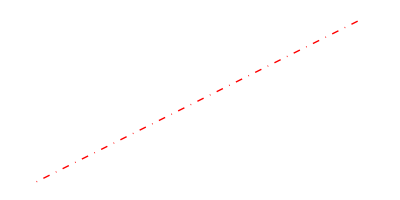

Dashing[{0,Small,Small,Small}]

-Graphics-

Dashing[None]

```mathematica
(* Total *)
Graphics[{Dashing[{0.05,0.01}],Red,Line[{{0,0},{2,1}}]}]
totLine=Dashing[{0.05,0.01}]
(* Ancestral *)
Graphics[{Dashing[Large],Red,Line[{{0,0},{2,1}}]}]
ansLine=Dashing[Large]
(* Infected *)
Graphics[{Dashing[{0.002,0.003}],Thick,Red,Line[{{0,0},{2,1}}]}]
infLine={Dashing[{0.002,0.003}],Thick}
(* Single mutant *)
Graphics[{Dashing[None],Red,Line[{{0,0},{2,1}}]}]
smLine=Dashing[None]
(* Double mutant *)
Graphics[{DotDashed,Red,Line[{{0,0},{2,1}}]}]
dmLine=DotDashed
(* Phage *)
Graphics[{Dashing[None],Red,Line[{{0,0},{2,1}}]}]
pline=Dashing[None]
```

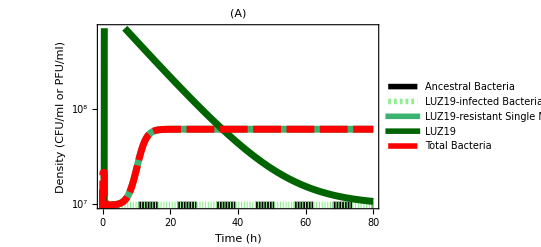

```mathematica
Plot[Evaluate[soldelay[0.8772547720626924,0.017,0.9,460,100,26/60,0.09,0.77,0.2,1]],{t,-1,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},Frame->True,FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","LUZ19-infected\nBacteria","LUZ19-resistant\nSingle Mutant","LUZ19","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,ansLine,AbsoluteThickness[5]},{RGBColor["lightgreen"],infLine,AbsoluteThickness[5]},{RGBColor["mediumseagreen"],smLine,AbsoluteThickness[5]},{RGBColor["darkgreen"],pline,AbsoluteThickness[5]},{Red,totLine,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(A)"]
```

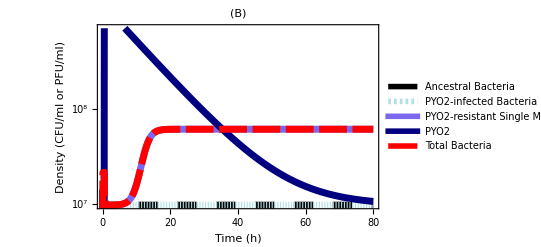

```mathematica
Plot[Evaluate[soldelay[0.8772547720626924,0.005,0.9,460,100,26/60,0.09,0.8,0.2,1]],{t,-1,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","PYO2-infected\nBacteria","PYO2-resistant\nSingle Mutant","PYO2","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,ansLine,AbsoluteThickness[5]},{RGBColor["powderblue"],infLine,AbsoluteThickness[5]},{RGBColor["mediumslateblue"],smLine,AbsoluteThickness[5]},{RGBColor["navy"],pline,AbsoluteThickness[5]},{Red,totLine,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(B)"]
```

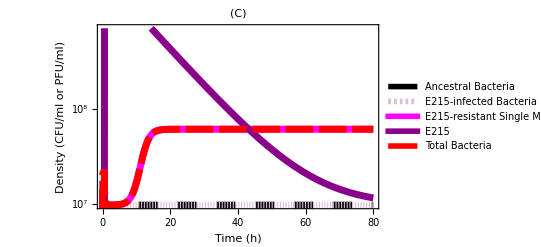

```mathematica
Plot[Evaluate[soldelay[0.8772547720626924,0.005,0.9,460,200,30.000000001/60,0.09,0.81,0.2,1]],{t,-1,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","E215-infected\nBacteria","E215-resistant\nSingle Mutant","E215","Total Bacteria"}],{0.79,0.6}],PlotStyle->{{Black,ansLine,AbsoluteThickness[5]},{RGBColor["thistle"],infLine,AbsoluteThickness[5]},{RGBColor["magenta"],smLine,AbsoluteThickness[5]},{RGBColor["darkmagenta"],pline,AbsoluteThickness[5]},{Red,totLine,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(C)"]
```

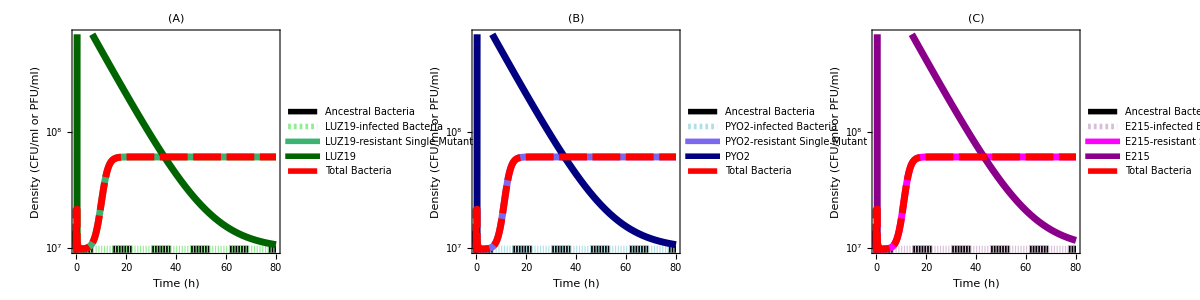

```mathematica
Minimize[a/(b*P0+a)*B0*E^(rr*t)+(b*P0)/(b*P0+a)*B0*E^(-s*t),t]
```

Minimize[(a B0 ⅇ^(rr t))/(a+b P0)+(b B0 ⅇ^(-s t) P0)/(a+b P0),t]

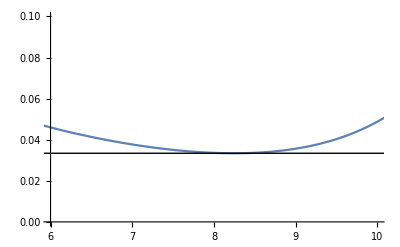

```mathematica
Plot[Evaluate[a/(b*P0+a)*B0*E^(rr*t)+(b*P0)/(b*P0+a)*B0*E^(-s*t)/.{a->0.005,b->460,P0->0.2,B0->0.2,rr->0.8,s->0.25}],{t,0,20},PlotRange->{{6,10},{0,0.1}},Epilog->{Line[{{0,0.033415402351083756},{20,0.033415402351083756}}]}]
```

```mathematica
f[t_]:=a/(b*P0+a)*B0*E^(rr*t)+(b*P0)/(b*P0+a)*B0*E^(-s*t)
```

```mathematica
(f[t]/.Solve[f'[t]==0,t])/.{a->0.005,b->460,P0->0.2,B0->0.2,rr->0.8,s->0.25}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{0.0334154}

```mathematica
Solve[f'[t]==0,t]/.{a->0.005,b->460,P0->0.2,B0->0.2,rr->0.8,s->0.25}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→8.24472}}

```mathematica
Solve[f'[t]==0,t]/.{a->0.027,b->460,P0->0.2,B0->0.2,rr->0.77,s->0.19}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→7.01494}}

```mathematica
Solve[f'[t]==0,t]/.{a->0.005,b->460,P0->0.2,B0->0.2,rr->0.81,s->0.02}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→7.37205}}

```mathematica
FullSimplify[f[t]/.Solve[f'[t]==0,t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{(a B0 ((a rr)/(b P0 s))^(-rr/(rr+s)) (rr+s))/((a+b P0) s)}

```mathematica
Solve[f'[t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-Log[(a rr)/(b P0 s)]/(rr+s)}}

```mathematica
f'[t]
```

(a B0 ⅇ^(rr t) rr)/(a+b P0)-(b B0 ⅇ^(-s t) P0 s)/(a+b P0)

```mathematica
PH2[a_,k_,b_,h_,s_,p_,ra_]={rn*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+ra*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+ra*Br*(1-(B+Br)/k)};
```

```mathematica
FullSimplify[rn*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+ra*Br*(1-(B+Br)/k)==0]
```

((B+Br-k) (Br ra+B rn))/k+Bi s==0

## Lowest bacteria concentration

```mathematica
FullSimplify[0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-0.005*B+a*Br-s*Bi+b*B*P+0.005*B+0.8*Br*(1-(B+Br)/k)-a*Br]
```

0.-(0.877255 B (B+Br-1. k))/k-(0.8 Br (B+Br-1. k))/k-Bi s

### s and h

```mathematica
CFU[x_]:=57115528.37x+9785470.84
```

{{2.12086×10^7,1.83612×10^7,1.57713×10^7,1.40022×10^7,1.28093×10^7,1.19974×10^7,1.14355×10^7,1.10397×10^7,1.07555×10^7,1.05479×10^7},{2.12086×10^7,1.82871×10^7,1.56858×10^7,1.39191×10^7,1.27344×10^7,1.19321×10^7,1.13797×10^7,1.09921×10^7,1.0715×10^7,1.05134×10^7},{2.17419×10^7,1.82403×10^7,1.56307×10^7,1.38656×10^7,1.26862×10^7,1.18902×10^7,1.13438×10^7,1.09616×10^7,1.06892×10^7,1.04914×10^7},{2.1689×10^7,1.82059×10^7,1.559×10^7,1.38259×10^7,1.26505×10^7,1.18592×10^7,1.13174×10^7,1.09392×10^7,1.06702×10^7,1.04753×10^7},{2.16557×10^7,1.81786×10^7,1.55576×10^7,1.37942×10^7,1.2622×10^7,1.18346×10^7,1.12964×10^7,1.09214×10^7,1.06551×10^7,1.04625×10^7},{2.16321×10^7,1.81559×10^7,1.55306×10^7,1.37678×10^7,1.25983×10^7,1.18141×10^7,1.12789×10^7,1.09067×10^7,1.06427×10^7,1.0452×10^7},{2.16141×10^7,1.81366×10^7,1.55074×10^7,1.37452×10^7,1.2578×10^7,1.17966×10^7,1.1264×10^7,1.08941×10^7,1.06321×10^7,1.04431×10^7},{2.15997×10^7,1.81197×10^7,1.54871×10^7,1.37255×10^7,1.25603×10^7,1.17812×10^7,1.12511×10^7,1.08832×10^7,1.06229×10^7,1.04353×10^7},{2.15878×10^7,1.81046×10^7,1.54691×10^7,1.37078×10^7,1.25446×10^7,1.17676×10^7,1.12395×10^7,1.08735×10^7,1.06147×10^7,1.04284×10^7},{2.15777×10^7,1.80911×10^7,1.54527×10^7,1.3692×10^7,1.25304×10^7,1.17554×10^7,1.12292×10^7,1.08647×10^7,1.06074×10^7,1.04222×10^7}}

{{10,0.001,2.12086×10^7},{10,0.051,1.83612×10^7},{10,0.101,1.57713×10^7},{10,0.151,1.40022×10^7},{10,0.201,1.28093×10^7},{10,0.251,1.19974×10^7},{10,0.301,1.14355×10^7},{10,0.351,1.10397×10^7},{10,0.401,1.07555×10^7},{10,0.451,1.05479×10^7},{40,0.001,2.12086×10^7},{40,0.051,1.82871×10^7},{40,0.101,1.56858×10^7},{40,0.151,1.39191×10^7},{40,0.201,1.27344×10^7},{40,0.251,1.19321×10^7},{40,0.301,1.13797×10^7},{40,0.351,1.09921×10^7},{40,0.401,1.0715×10^7},{40,0.451,1.05134×10^7},{70,0.001,2.17419×10^7},{70,0.051,1.82403×10^7},{70,0.101,1.56307×10^7},{70,0.151,1.38656×10^7},{70,0.201,1.26862×10^7},{70,0.251,1.18902×10^7},{70,0.301,1.13438×10^7},{70,0.351,1.09616×10^7},{70,0.401,1.06892×10^7},{70,0.451,1.04914×10^7},{100,0.001,2.1689×10^7},{100,0.051,1.82059×10^7},{100,0.101,1.559×10^7},{100,0.151,1.38259×10^7},{100,0.201,1.26505×10^7},{100,0.251,1.18592×10^7},{100,0.301,1.13174×10^7},{100,0.351,1.09392×10^7},{100,0.401,1.06702×10^7},{100,0.451,1.04753×10^7},{130,0.001,2.16557×10^7},{130,0.051,1.81786×10^7},{130,0.101,1.55576×10^7},{130,0.151,1.37942×10^7},{130,0.201,1.2622×10^7},{130,0.251,1.18346×10^7},{130,0.301,1.12964×10^7},{130,0.351,1.09214×10^7},{130,0.401,1.06551×10^7},{130,0.451,1.04625×10^7},{160,0.001,2.16321×10^7},{160,0.051,1.81559×10^7},{160,0.101,1.55306×10^7},{160,0.151,1.37678×10^7},{160,0.201,1.25983×10^7},{160,0.251,1.18141×10^7},{160,0.301,1.12789×10^7},{160,0.351,1.09067×10^7},{160,0.401,1.06427×10^7},{160,0.451,1.0452×10^7},{190,0.001,2.16141×10^7},{190,0.051,1.81366×10^7},{190,0.101,1.55074×10^7},{190,0.151,1.37452×10^7},{190,0.201,1.2578×10^7},{190,0.251,1.17966×10^7},{190,0.301,1.1264×10^7},{190,0.351,1.08941×10^7},{190,0.401,1.06321×10^7},{190,0.451,1.04431×10^7},{220,0.001,2.15997×10^7},{220,0.051,1.81197×10^7},{220,0.101,1.54871×10^7},{220,0.151,1.37255×10^7},{220,0.201,1.25603×10^7},{220,0.251,1.17812×10^7},{220,0.301,1.12511×10^7},{220,0.351,1.08832×10^7},{220,0.401,1.06229×10^7},{220,0.451,1.04353×10^7},{250,0.001,2.15878×10^7},{250,0.051,1.81046×10^7},{250,0.101,1.54691×10^7},{250,0.151,1.37078×10^7},{250,0.201,1.25446×10^7},{250,0.251,1.17676×10^7},{250,0.301,1.12395×10^7},{250,0.351,1.08735×10^7},{250,0.401,1.06147×10^7},{250,0.451,1.04284×10^7},{280,0.001,2.15777×10^7},{280,0.051,1.80911×10^7},{280,0.101,1.54527×10^7},{280,0.151,1.3692×10^7},{280,0.201,1.25304×10^7},{280,0.251,1.17554×10^7},{280,0.301,1.12292×10^7},{280,0.351,1.08647×10^7},{280,0.401,1.06074×10^7},{280,0.451,1.04222×10^7}}

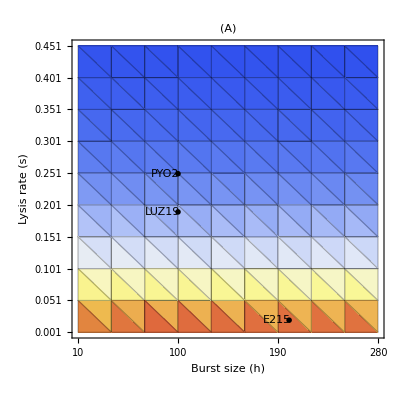

```mathematica
Module[{i,j,l,parameterValues,sol},
PH2[k_,b_,s_,h_,p_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-0.005*B,-s*Bi+b*B*P,0.005*B+0.8*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-s*Bi+0.8*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
result=Table[Table[NA,10],10];
For[i=0,i<10,i=i+1,
For[j=0,j<10,j=j+1,
parameterValues={k->0.9,b->460,s->0.001+0.05*j,h->40+i*30,p->0.09};
sol=NDSolveValue[{{X'[t]==(PH2[k,b,s,h,p]/.Thread[stateVar->X[t]])/.parameterValues},X[0]=={0.2,0,0,0.2,0.2}},CFU[Bt[t]],{t,0,50}];
totMin=FindMinimum[{sol,0<=t<=30},{t,10}];
result[[i+1,j+1]]=totMin[[1]]
]
];
result
]
Module[{i,j,k},
heatResult=Table[Table[{NA,NA,NA},10],10];
finalResult={};
For[i=1,i≤10,i++,
For[j=1,j≤10,j++,
heatResult[[i,j,1]]=10+(i-1)*30;
heatResult[[i,j,2]]=0.001+0.005*(j-1)*10;
heatResult[[i,j,3]]=result[[i,j]];
]
];
For[k=1,k≤10,k++,
finalResult=Join[finalResult,heatResult[[k]]]
];
finalResult
]
g1=Show[ListDensityPlot[finalResult,Mesh->All,PlotTheme->"Detailed",BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Burst size (h)","Lysis rate (s)"},ImageSize->Full,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Minimal total bacterial density (CFU/ml)",LabelStyle->{Italic,Bold,Black,FontFamily->"Helvetica"}],Above],ColorFunction->"TemperatureMap",FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},FrameTicks->{{Table[0.001+0.005*j,{j,0,90,10}],None},{Table[40+i*30,{i,-1,9,1}],None}},PlotRange->All,Epilog->{Text["LUZ19",{86,0.19}],Text["PYO2",{88,0.25}],Text["E215",{189,0.02}]},PlotLabel->"(A)"],Graphics[{PointSize[0.01],Point[{{100,0.19},{100,0.25},{200,0.02}}]}]]
```

```mathematica
minDense[0.005,0.8,0.01,460,0.2,0.2]
```

2.05998×10^7

{{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7}}

{{10,0.001,2.11776×10^7},{10,0.051,1.77408×10^7},{10,0.101,1.51814×10^7},{10,0.151,1.35064×10^7},{10,0.201,1.24108×10^7},{10,0.251,1.16821×10^7},{10,0.301,1.11869×10^7},{10,0.351,1.0843×10^7},{10,0.401,1.0599×10^7},{10,0.451,1.04225×10^7},{40,0.001,2.11776×10^7},{40,0.051,1.77408×10^7},{40,0.101,1.51814×10^7},{40,0.151,1.35064×10^7},{40,0.201,1.24108×10^7},{40,0.251,1.16821×10^7},{40,0.301,1.11869×10^7},{40,0.351,1.0843×10^7},{40,0.401,1.0599×10^7},{40,0.451,1.04225×10^7},{70,0.001,2.11776×10^7},{70,0.051,1.77408×10^7},{70,0.101,1.51814×10^7},{70,0.151,1.35064×10^7},{70,0.201,1.24108×10^7},{70,0.251,1.16821×10^7},{70,0.301,1.11869×10^7},{70,0.351,1.0843×10^7},{70,0.401,1.0599×10^7},{70,0.451,1.04225×10^7},{100,0.001,2.11776×10^7},{100,0.051,1.77408×10^7},{100,0.101,1.51814×10^7},{100,0.151,1.35064×10^7},{100,0.201,1.24108×10^7},{100,0.251,1.16821×10^7},{100,0.301,1.11869×10^7},{100,0.351,1.0843×10^7},{100,0.401,1.0599×10^7},{100,0.451,1.04225×10^7},{130,0.001,2.11776×10^7},{130,0.051,1.77408×10^7},{130,0.101,1.51814×10^7},{130,0.151,1.35064×10^7},{130,0.201,1.24108×10^7},{130,0.251,1.16821×10^7},{130,0.301,1.11869×10^7},{130,0.351,1.0843×10^7},{130,0.401,1.0599×10^7},{130,0.451,1.04225×10^7},{160,0.001,2.11776×10^7},{160,0.051,1.77408×10^7},{160,0.101,1.51814×10^7},{160,0.151,1.35064×10^7},{160,0.201,1.24108×10^7},{160,0.251,1.16821×10^7},{160,0.301,1.11869×10^7},{160,0.351,1.0843×10^7},{160,0.401,1.0599×10^7},{160,0.451,1.04225×10^7},{190,0.001,2.11776×10^7},{190,0.051,1.77408×10^7},{190,0.101,1.51814×10^7},{190,0.151,1.35064×10^7},{190,0.201,1.24108×10^7},{190,0.251,1.16821×10^7},{190,0.301,1.11869×10^7},{190,0.351,1.0843×10^7},{190,0.401,1.0599×10^7},{190,0.451,1.04225×10^7},{220,0.001,2.11776×10^7},{220,0.051,1.77408×10^7},{220,0.101,1.51814×10^7},{220,0.151,1.35064×10^7},{220,0.201,1.24108×10^7},{220,0.251,1.16821×10^7},{220,0.301,1.11869×10^7},{220,0.351,1.0843×10^7},{220,0.401,1.0599×10^7},{220,0.451,1.04225×10^7},{250,0.001,2.11776×10^7},{250,0.051,1.77408×10^7},{250,0.101,1.51814×10^7},{250,0.151,1.35064×10^7},{250,0.201,1.24108×10^7},{250,0.251,1.16821×10^7},{250,0.301,1.11869×10^7},{250,0.351,1.0843×10^7},{250,0.401,1.0599×10^7},{250,0.451,1.04225×10^7},{280,0.001,2.11776×10^7},{280,0.051,1.77408×10^7},{280,0.101,1.51814×10^7},{280,0.151,1.35064×10^7},{280,0.201,1.24108×10^7},{280,0.251,1.16821×10^7},{280,0.301,1.11869×10^7},{280,0.351,1.0843×10^7},{280,0.401,1.0599×10^7},{280,0.451,1.04225×10^7}}

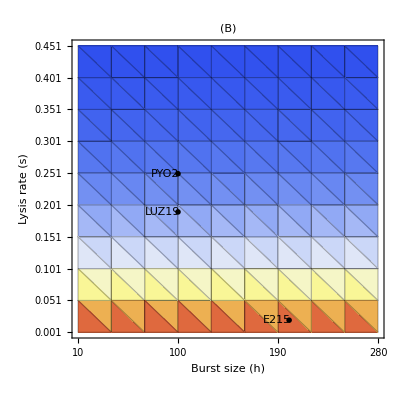

```mathematica
minDense[a_,rr_,s_,b_,B0_,P0_]:=CFU[(a B0 ((a rr)/(b P0 s))^(-rr/(rr+s)) (rr+s))/((a+b P0) s)]
Module[{i,j,l,parameterValues,sol},
PH2[k_,b_,s_,h_,p_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-0.005*B,-s*Bi+b*B*P,0.005*B+0.8*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-s*Bi+0.8*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
result=Table[Table[NA,10],10];
For[i=0,i<10,i=i+1,
For[j=0,j<10,j=j+1,
parameterValues={k->0.9,b->460,s->0.001+0.05*j,h->40+i*30,p->0.09,rr->0.8,a->0.005};
totMin=minDense[a,rr,0.001+0.05*j,b,0.2,0.2]/.parameterValues;
result[[i+1,j+1]]=totMin
]
];
result
]
Module[{i,j,k},
heatResult=Table[Table[{NA,NA,NA},10],10];
finalResult={};
For[i=1,i≤10,i++,
For[j=1,j≤10,j++,
heatResult[[i,j,1]]=10+(i-1)*30;
heatResult[[i,j,2]]=0.001+0.005*(j-1)*10;
heatResult[[i,j,3]]=result[[i,j]];
]
];
For[k=1,k≤10,k++,
finalResult=Join[finalResult,heatResult[[k]]]
];
finalResult
]
g2=Show[ListDensityPlot[finalResult,Mesh->All,PlotTheme->"Detailed",BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Burst size (h)","Lysis rate (s)"},ImageSize->Full,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Minimal total bacterial density (CFU/ml)",LabelStyle->{Italic,Bold,Black,FontFamily->"Helvetica"}],Above],ColorFunction->"TemperatureMap",FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},FrameTicks->{{Table[0.001+0.005*j,{j,0,90,10}],None},{Table[40+i*30,{i,-1,9,1}],None}},PlotRange->All,Epilog->{Text["LUZ19",{86,0.19}],Text["PYO2",{88,0.25}],Text["E215",{189,0.02}]},PlotLabel->"(B)"],Graphics[{PointSize[0.01],Point[{{100,0.19},{100,0.25},{200,0.02}}]}]]
```

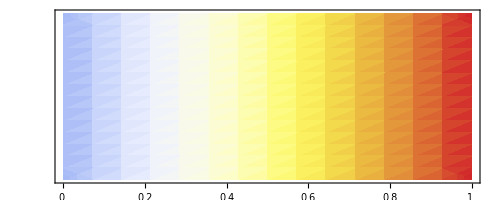

```mathematica
colorbar[cf_]:=DensityPlot[x,{x,0,370},{y,0,50},ColorFunction->cf,ColorFunctionScaling->True,AspectRatio->Automatic,PlotRangePadding->10,FrameTicks->{{None,None},{Transpose[{Subdivide[370,5],N@Subdivide[5]}],None}}]
cf=ColorData["TemperatureMap",Rescale[#,{0,1},{0.25,1}]]&;
colorbar[cf]
```

```mathematica
g2[[2,1]]
```

```mathematica
GraphicsGrid[{{g1,g2}},ImageSize->2000]
```

-Graphics-

### Countour s, a, b,rr

```mathematica
minDense[a_,rr_,s_,b_,B0_,P0_]
```

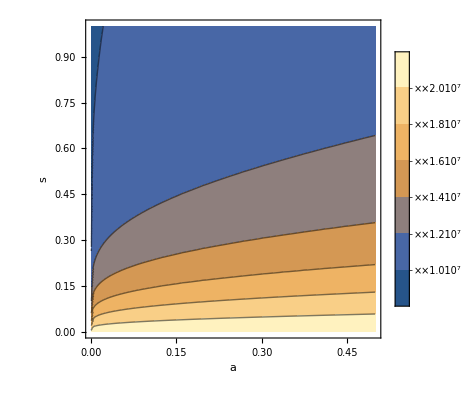

```mathematica
ContourPlot[minDense[a,0.8,s,460,0.2,0.2],{a,0,0.5},{s,0,1},PlotLegends->Automatic,FrameLabel->Automatic]
```

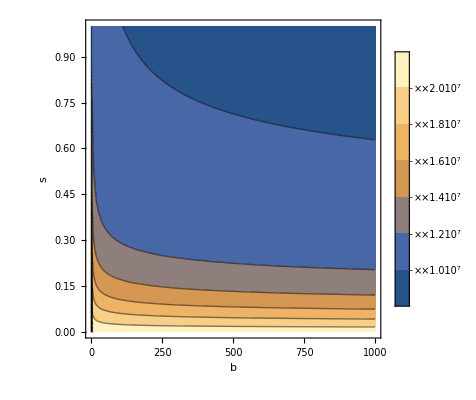

```mathematica
ContourPlot[minDense[0.005,0.8,s,b,0.2,0.2],{b,0,1000},{s,0,1},PlotLegends->Automatic,FrameLabel->Automatic]
```

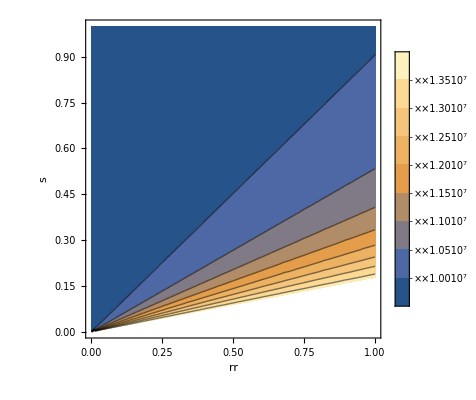

```mathematica
ContourPlot[minDense[0.005,rr,s,460,0.2,0.2],{rr,0,1},{s,0,1},PlotLegends->Automatic,FrameLabel->Automatic]
```

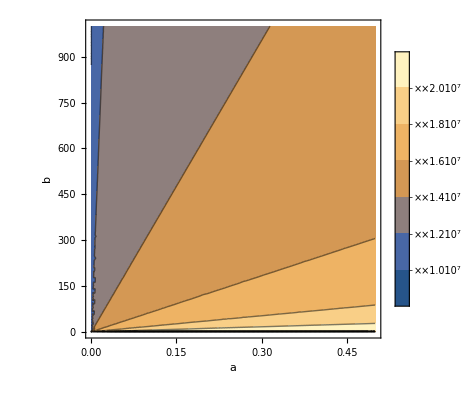

```mathematica
ContourPlot[minDense[a,0.8,0.252,b,0.2,0.2],{a,0,0.5},{b,0,1000},PlotLegends->Automatic,FrameLabel->Automatic]
```

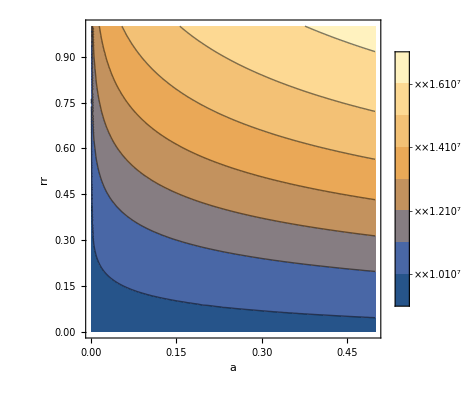

```mathematica
ContourPlot[minDense[a,rr,0.252,460,0.2,0.2],{a,0,0.5},{rr,0,1},PlotLegends->Automatic,FrameLabel->Automatic]
```

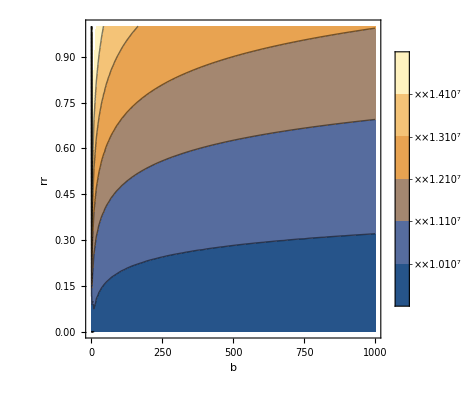

```mathematica
ContourPlot[minDense[0.005,rr,0.252,b,0.2,0.2],{b,0,1000},{rr,0,1},PlotLegends->Automatic,FrameLabel->Automatic]
```